# Non-Additive Probability Measures

## Compatibility to Mathematica 9.0

```mathematica
If[Attributes[AllTrue]=={},
AllTrue[list_List,test_]:=Catch[
Do[If[¬test[A],Throw[False]],{A,list}];
True];
Attributes[AllTrue]={Protected}]
```

```mathematica
AllTrue[{22,25,26},MemberQ[{},#]&]
```

False

```mathematica
If[Attributes[SubsetQ]=={},
SubsetQ[list1_List,list2_List]:=AllTrue[list2,MemberQ[list1,#]&];
Attributes[SubsetQ]={Protected}]
```

```mathematica
SubsetQ[{},{22,25,26}]
```

False

```mathematica
If[Attributes[FirstPosition]=={},
FirstPosition[expr_,pattern_]:=First[Position[expr,pattern]];
Attributes[FirstPosition]={Protected}]
```

```mathematica
listQWhy[listFunction_]:={listFunction,Apply[And,listFunction[##],{0,2}]&,Module[{f},
f[X_,v_,μ_,g_:Function[{col,μ,v},col/.μ->v]]:=Column[#==g[#,μ,v]&/@Select[listFunction[X,μ],¬g[#,μ,v]&]];
f]}
```

```mathematica
(*http://forums.wolfram.com/mathgroup/archive/2006/Jan/msg00020.html*)
WithX[{},E_]:=E
WithX[{a_,b___},E_]:=With[{a},WithX[{b},E]]
Attributes[WithX]={HoldAll}
WithX[{x=1},x]
WithX[{x=1,y=x+1},{y,x}]
```

{HoldAll}

1

{2,1}

## S. Graf, A Radon-Nikodym Theorem for Capacities

The following function verifies whether a given function is capacity or not.
Defintion

∀A∈𝔘,v(A)≥0

v(∅)=0

∀A, B∈𝔘, v(A∪B)≤v(A)+v(B)

∀A, B∈𝔘, A⊆B⇒v(A)≤v(B)

For every increasing sequence (A_n)_(n∈ℕ) in 𝔘 the equality v(∪_(n∈ℕ)A_n)=lim_(n→∞) v(A_n) holds. 
(Need not to verify in finite case.)

```mathematica
capacityOtherList[X_,v_]:=Join[v[#]≥0&/@Subsets[X],{v[{}]==0},Flatten[Table[v[A∪B]≤v[A]+v[B],{A,Subsets[X]},{B,Subsets[Complement[X,A]]}]]]
capacityMonotoneList[X_,v_]:=Flatten[Table[v[A]≤v[B],{B,Subsets[X]},{A,Subsets[B]}]]
```

```mathematica
{capacityList,capacityQ,capacityWhy}=listQWhy[Function[{X,v},Join[capacityOtherList[X,v],capacityMonotoneList[X,v]]]];
```

## L. Shapley, Notes on n-Person Games VII: Cores of Convex Games

The following function verifies whether a given function is capacity or not.
Defintion

∀A∈𝔘,v(A)≥0

v(∅)=0

∀A, B∈𝔘, v(A)+v(B)≤v(A∪B)

```mathematica
{gameList,gameQ,gameWhy}=listQWhy[Function[{N,v},Join[v[#]≥0&/@Subsets[N],{v[{}]==0},Flatten[Table[v[A∪B]≥v[A]+v[B],{A,Subsets[N]},{B,Subsets[Complement[N,A]]}]]]]];
```

```mathematica
{convexList,convexQ,convexWhy}=listQWhy[Function[{N,v},Flatten[Table[v[A∪B]+v[A∩B]≥v[A]+v[B],{A,Subsets[N]},{B,Subsets[N]}]]]];
```

```mathematica
radonNikodymDerivative2Measure[f_]:=Function[{S},Total[f/@S]]
```

```mathematica
S[N_,ω_,k_]:=Select[N,ω[#]≤k&]
a[N_,v_,ω_]:=Function[{i},v[S[N,ω,ω[i]]]-v[S[N,ω,ω[i]-1]]]
aMeasure[N_,v_,ω_]:=radonNikodymDerivative2Measure[a[N,v,ω]]
```

```mathematica
ShapleyValue[N_,v_]:=Function[{i},Total[Table[(Length[S]!(Length[N]-Length[S]-1)!)/(Length[N]!)(v[Append[S,i]]-v[S]),{S,Subsets[Complement[N,{i}]]}]]]
```

```mathematica
ShapleyValueMeasure[N_,v_]:=radonNikodymDerivative2Measure[ShapleyValue[N,v]]
Module[{N={1,2,3},v=Function[{S},If[MemberQ[S,1],If[S=={1},0,1],0]]},ShapleyValueMeasure[N,v]/@Subsets[N]]
ShapleyValue[{a},l][a]
a[{a},l,1&][a]
```

{0,2/3,1/6,1/6,5/6,5/6,1/3,1}

-l[{}]+l[{a}]

-l[{}]+l[{a}]

## K. Jamison, W. Lodwick, Interval-Valued Probability Measures

This file verifies interval-valued probability measures in prob.tex.

```mathematica
interval2LeftEnd[int_interval]:=int⟦1,1⟧(*Min*)
```

```mathematica
interval2RightEnd[int_interval]:=int⟦1,2⟧(*Max*)
```

```mathematica
IVPM2Game[i_]:=interval2LeftEnd[i[#]]&
```

```mathematica
IVPM2Capacity[i_]:=interval2RightEnd[i[#]]&
```

```mathematica
complement[X_List,v_]:=1-v[Complement[X,#]]&
```

```mathematica
game2IVPM[S_,v_]:=interval[{v[#],complement[S,v][#]}]&(*Because we don't know whether v[#]≤complement[S,v][#] yet. If we use the build-in Interval, Mathematica may switch {v[#],complement[S,v][#]}, and the code to verify whether *)
```

```mathematica
capacity2IVPM[S_,v_]:=interval[{complement[S,v][#],v[#]}]&
```

```mathematica
possibilityDistributionFunction2Capacity[p_]:=(Max @@Append[p/@#,0])&
```

```mathematica
necessityDistributionFunction2Game[S_,n_]:=(Min@@Append[n/@Complement[S,#],1])&
```

The following function verifies whether a given function is an interval-valued probability measure or not by following Jamison & Lodwick (2004)1. However, their defintion is both conceptual or computational complex. Therefore, we are going to verify the following definition instead.
Defintion

∀A∈𝒜,i_m(A)=[a^-(A),a^+(A)] and a^+ is a capacity  a^- is a game

a^+(S)=1

a^+(A)=1-a^-(A^c)

The equivalence of two definitions are trivial so we omit the proof here.

```mathematica
IVPMComplementList[S_,vl_,vr_]:=vr[#]==complement[S,vl][#]&/@Subsets[S]
{IVPMList,IVPMQ,IVPMWhy}=listQWhy[Function[{S,i},With[{vl=IVPM2Game[i],vr=IVPM2Capacity[i]},Join[gameList[S,vl],capacityOtherList[S,vr],IVPMComplementList[S,vl,vr]]]]];
```

```mathematica
consistentList[S_,i_,P_]:=interval2LeftEnd[i[#]]≤P[#]≤interval2RightEnd[i[#]]&/@Subsets[S]
consistentQ[S_,i_,P_]:=Apply[And,consistentList[S,i,P],{0,2}]
consistentWhy[S_,i_,P_]:=Column[MapThread[Equal,{Flatten[consistentList[S,i,P]],Flatten[consistentList[S,μ,v]]}]]
```

```mathematica
coreCondition[Ω_,ρ_,l_,r_]:=consistentList[Ω,interval[{l[#],r[#]}]&,radonNikodymDerivative2Measure[ρ]]
coreConditionWithoutEqual[Ω_,ρ_,l_,r_]:=With[{ρ1=If[#===Last[Ω],1-Total[ρ/@Most[Ω]],ρ[#]]&},coreCondition[Ω,ρ1,l,r]]
coreConditionAnd[Ω_,ρ_,l_,r_]:=Simplify[And@@coreCondition[Ω,ρ,l,r]]
coreConditionWithoutEqualAnd[Ω_,ρ_,l_,r_]:=Simplify[And@@coreConditionWithoutEqual[Ω,ρ,l,r]]
```

## A. Neumaier, Clouds, Fuzzy Sets, and Probability Intervals W. Lodwick, K. Jamison, Interval-valued Probability in the Analysis of Problems Containing a Mixture of Possibilistic, Probabilistic, and Interval Uncertainty

```mathematica
intersection[i1_,i2_]:=interval[{Max[interval2LeftEnd[i1[#]],interval2LeftEnd[i2[#]]],Min[interval2RightEnd[i1[#]],interval2RightEnd[i2[#]]]}]&
```

## M. Osborne, A. Rubinstein, A Course in Game Theory

```mathematica
Needs["Developer`"]
```

```mathematica
{balancedCollectionWeightsList,balancedCollectionWeightsQ,balancedCollectionWeightsWhy}=listQWhy[Function[{N,λ},Join[0≤λ[#]≤1&/@Subsets[N],Table[Total[λ[Append[#,i]]&/@Subsets[Complement[N,{i}]]]==1,{i,N}]]]];
```

```mathematica
With[{N=Range[3],λ=Boole[Length[#]==2]/2&},balancedCollectionWeightsQ[N,λ]]
With[{N=Range[3],λ=Boole[Length[#]==1]&},balancedCollectionWeightsQ[N,λ]]
```

True

True

```mathematica
balancedCondition[N_,v_,λ_]:=Total[λ[#]v[#]&/@Subsets[N]]≤v[N]
balancedQ[N_,v_]:=Block[{λ,balancedCollectionWeightsList1},
balancedCollectionWeightsList1=balancedCollectionWeightsList[N,λ];
balancedCollectionWeightsList1⟦0⟧=And;Resolve[ForAll[Evaluate[λ/@Subsets[N]],balancedCollectionWeightsList1,balancedCondition[N,v,λ]],Reals]]
```

```mathematica
nonEmptyCoreQ[Ω_,l_]:=Block[{ρ},Resolve[Exists[Evaluate[ρ/@Ω],coreConditionAnd[Ω,ρ,l,complement[Ω,l]]],Reals]]
```

```mathematica
findCoreInstance[Ω_,l_]:=Module[{ρ,rule},
rule=Flatten[FindInstance[coreConditionAnd[Ω,ρ,l,complement[Ω,l]],Evaluate[ρ/@Ω],Reals,RandomSeed->RandomInteger[$MaxMachineInteger]]];ρ[#]/.rule&]
```

## Dempster-Shafer Belief Function

```mathematica
Intersect[S_]:=If[Length[S]==0,{},Intersection@@S]
Intersect[{}]
```

{}

The following function verifies whether a given function is a Dempster-Shafer belief function or not by following Shafer (1976). 
Defintion

Bel(∅)=0

Bel(S)=1

∀{A_k}_(k=1)^n , Bel(∪_(k=1)^n A_k)≥∑_(I⊆{1,...,n}) (-1)^(|I|+1)Bel(∩_(i∈I)A_i)

```mathematica
If[Attributes[AllTrue]=={},AllTrue[list_List,test_]:=Module[{},Do[If[¬test[A],Return[False]],{A,list}];True];Attributes[AllTrue]={Protected}]
```

```mathematica
DempsterShaferBeliefList[S_List,Bel_]:={Bel[{}]==0,Bel[S]==1,0≤Bel[#]≤1&/@Subsets[S],Table[Bel[Union@@A]≥Total[(-1)^(Length[#]+1)Bel[Intersect[#]]&/@Subsets[A]],{A,Subsets[Subsets[S]]}]}
DempsterShaferBeliefQ[S_List,Bel_,OptionsPattern[{Speed->False}]]:=If[OptionValue[Speed],And[Bel[{}]==0,Bel[S]==1,AllTrue[Subsets[S],0≤Bel[#]≤1&],AllTrue[Subsets[Subsets[S]],Function[{A},Bel[Union@@A]≥Total[(-1)^(Length[#]+1)Bel[Intersect[#]]&/@Subsets[A]]]]],Apply[And,DempsterShaferBeliefList[S,Bel],{0,2}]]
DempsterShaferBeliefWhy[S_List,Bel_]:=Column[MapThread[Equal,{Flatten[DempsterShaferBeliefList[S,Bel]],Flatten[DempsterShaferBeliefList[S,μ]]}]]
```

## B. Peleg, An Inductive Method of Constructing Minimal Balanced Collections of Finite Sets

```mathematica
incidenceMatrix[n_Integer,b_]:=With[{N=Range[n],k=Length[b]},Array[Boole[MemberQ[b⟦#1⟧,#2]]&,{k,n}]]
incidenceMatrix[X_List,b_]:=incidenceMatrix[Length[X],Map[FirstPosition[X,#]⟦1⟧&,b,{-1}]]
incidenceMatrix[4,{{1,2},{3,4}}]//MatrixForm
incidenceMatrix[2,{{1},{2}}]//MatrixForm
incidenceMatrix[{a,b,c,d,e},{{b,d},{a,b,e},{a,c,d,e},{a,c,d},{b,c,e}}]//MatrixForm
```

(1 | 1 | 0 | 0
0 | 0 | 1 | 1)

(1 | 0
0 | 1)

(0 | 1 | 0 | 1 | 0
1 | 1 | 0 | 0 | 1
1 | 0 | 1 | 1 | 1
1 | 0 | 1 | 1 | 0
0 | 1 | 1 | 0 | 1)

```mathematica
(*{{b,d},{a,b,e},{a,c,d,e},{a,c,d},{b,c,e}},{1/3,1/3,2/3,1/3,0}*)
```

```mathematica
{balanceVectorList,balanceVectorQ,balanceVectorWhy}=listQWhy[Function[{n,b,c},Prepend[Positive/@c,c.incidenceMatrix[n,b]==ConstantArray[1,If[Head[n]===Integer,n,Length[n]]]]]];
balanceVectorQ[4,{{1,2},{3,4}},{1,1}]
balanceVectorQ[1,{{1}},{1}]
balanceVectorQ[{a,b,c,d,e},{{b,d},{a,b,e},{a,c,d,e},{a,c,d},{b,c,e}},{1/3,1/3,2/3,1/3,0}]
balanceVectorQ[{a,b,c,d,e},{{b,d},{a,b,e},{a,c,d,e},{a,c,d},{b,c,e}},{1/3,1/3,1/3,1/3,1/3}]
```

True

True

False

True

```mathematica
collectionIsBalancedQ[n_Integer,b_]:=Module[{c,k=Length[b]},Resolve[Exists[Evaluate[c/@Range[k]],And@@balanceVectorList[n,b,c/@Range[k]]],Reals]]
collectionIsBalancedQ[X_List,b_]:=collectionIsBalancedQ[Length[X],Map[FirstPosition[X,#]⟦1⟧&,b,{-1}]]
collectionIsBalancedQ[4,{{1,2},{3,4}}]
collectionIsBalancedQ[{a,b,c,d,e},{{b,d},{a,b,e},{a,c,d,e},{a,c,d},{b,c,e}}]
```

True

True

```mathematica
minimalBalancedCollectionQ[n_Integer,b_]:=MatrixRank[incidenceMatrix[n,b]]==Length[b]
minimalBalancedCollectionQ[X_List,b_]:=minimalBalancedCollectionQ[Length[X],Map[FirstPosition[X,#]⟦1⟧&,b,{-1}]]
minimalBalancedCollectionQ[4,{{1,2},{3,4}}]
minimalBalancedCollectionQ[1,{{1}}]
minimalBalancedCollectionQ[{a,b,c,d,e},{{b,d},{a,b,e},{a,c,d,e},{a,c,d},{b,c,e}}]
```

True

True

True

```mathematica
extensionVectors[k_Integer]:=Flatten/@Tuples[{Tuples[{{0,0},{1,0},{1,1}},k],{0,1}}]
extensionVectors[b_List]:=extensionVectors[Length[b]]
extensionVectors[{{1,2},{3,4}}]
extensionVectors[{{1}}]
extensionVectors[{{1},{2}}]
```

{{0,0,0,0,0},{0,0,0,0,1},{0,0,1,0,0},{0,0,1,0,1},{0,0,1,1,0},{0,0,1,1,1},{1,0,0,0,0},{1,0,0,0,1},{1,0,1,0,0},{1,0,1,0,1},{1,0,1,1,0},{1,0,1,1,1},{1,1,0,0,0},{1,1,0,0,1},{1,1,1,0,0},{1,1,1,0,1},{1,1,1,1,0},{1,1,1,1,1}}

{{0,0,0},{0,0,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}}

{{0,0,0,0,0},{0,0,0,0,1},{0,0,1,0,0},{0,0,1,0,1},{0,0,1,1,0},{0,0,1,1,1},{1,0,0,0,0},{1,0,0,0,1},{1,0,1,0,0},{1,0,1,0,1},{1,0,1,1,0},{1,0,1,1,1},{1,1,0,0,0},{1,1,0,0,1},{1,1,1,0,0},{1,1,1,0,1},{1,1,1,1,0},{1,1,1,1,1}}

```mathematica
extension[n_Integer,b_,x_]:=With[{t=Table[ReleaseHold[Switch[x⟦{2i-1,2i}⟧,{0,0},b⟦i⟧,{1,0},HoldComplete[Append[b⟦i⟧,n+1],b⟦i⟧],{1,1},Append[b⟦i⟧,n+1]]],{i,Length[b]}]},If[Last[x]==1,Append[t,{n+1}],t]]
extension[X_List,b_,x_]:=extension[Length[X],Map[FirstPosition[X,#]⟦1⟧&,b,{-1}],x]
extension[1,{{1}},{0,0,1}]
```

{{1},{2}}

```mathematica
minimalBalancedCollectionsWithBalancingVector[n1_Integer]:=minimalBalancedCollectionsWithBalancingVector[n1]=Switch[n1,
0,{{},{}},
1,{{{{1}},{1}}},
_,
Module[{m,m1,m2,M1={},x,i,b,c,k,S1,T1,cz,b1,b2,c1,c2,z1,d,t},
WithX[{n=n1-1,
M=minimalBalancedCollectionsWithBalancingVector[n],
S=Function[{k,x},Select[Range[k],x⟦2#-1⟧==x⟦2#⟧&]],
T=Function[{k,x},Complement[Range[k],S[k,x]]],
z=Function[{x,i},x⟦2i-1⟧]},
Do[
b=m⟦1⟧;
c=m⟦2⟧;
k=Length[b];
Do[
S1=S[k,x];
T1=T[k,x];
cz=∑_i^S1 c⟦i⟧z[x,i];
Which[
x⟦2k+1⟧==1∧T1=={}∧cz<1,
AppendTo[M1,{extension[n,b,x],Append[c,1-cz]}],
x⟦2k+1⟧==0∧T1≠{}∧Length[S1]==k-1∧1>cz>1-c⟦T1⟦1⟧⟧,
AppendTo[M1,{extension[n,b,x],ReplacePart[c,T1⟦1⟧->Sequence[1-cz,c⟦T1⟦1⟧⟧-(1-cz)]]}](*Notice that becaues the index compute wrong in the original paper, this case doesn't follow the original paper.*),
x⟦2k+1⟧==0∧T1=={}∧cz==1,
AppendTo[M1,{extension[n,b,x],c}]],{x,extensionVectors[k]}],{m,M}];
Do[
b1=m1⟦1⟧;
b2=m2⟦1⟧;
b=b1∪b2;
k=Length[b];
c1=Table[If[MemberQ[b1,b⟦i⟧],Extract[m1⟦2⟧,FirstPosition[b1,b⟦i⟧]],0],{i,k}];
c2=Table[If[MemberQ[b2,b⟦i⟧],Extract[m2⟦2⟧,FirstPosition[b2,b⟦i⟧]],0],{i,k}];
If[MatrixRank[incidenceMatrix[n,b]]==k-1,
Do[If[x⟦2k+1⟧==0∧T[k,x]=={},
z1=Table[z[x,i],{i,k}];
d=(c2-c1).z1;
If[d≠0,
t=(1-c1.z1)/d;
If[0<t<1,
AppendTo[M1,{extension[n,b,x],(1-t)c1+t c2}]]]],{x,extensionVectors[k]}]],{m1,M},{m2,M}];
M1]]]
minimalBalancedCollectionsWithBalancingVector[X_List]:=minimalBalancedCollectionsWithBalancingVector[X]={Map[X⟦#⟧&,#⟦1⟧,{2}],#⟦2⟧}&/@minimalBalancedCollectionsWithBalancingVector[Length[X]]
minimalBalancedCollectionsWithBalancingVector[1]
minimalBalancedCollectionsWithBalancingVector[{a}]
minimalBalancedCollectionsWithBalancingVector[2]
minimalBalancedCollectionsWithBalancingVector[{a,b}]
```

{{{{1}},{1}}}

{{{{a}},{1}}}

{{{{1},{2}},{1,1}},{{{1,2}},{1}}}

{{{{a},{b}},{1,1}},{{{a,b}},{1}}}

## L. Shapley, On Balanced Sets and Cores

```mathematica
{properList,properQ,properWhy}=listQWhy[Function[{S},Flatten[Table[S⟦i⟧∩S⟦j⟧≠{},{i,Length[S]},{j,i-1}]]]];
```

```mathematica
Needs["Combinatorica`"]
minimalBalancedCollectionsWithBalancingVectorTest[n_]:=Module[{p=SetPartitions[n],bs=minimalBalancedCollectionsWithBalancingVector[n],b1,fS,r,t},
b1=First/@bs;
fS=p∪b1;
t=SortBy[Table[With[{c=Extract[bs,FirstPosition[b1,r]]⟦2⟧},{r,MemberQ[p,r],c,collectionIsBalancedQ[n,r],minimalBalancedCollectionQ[n,r],properQ[r],balanceVectorQ[n,r,c]}],{r,fS}],{¬#⟦2⟧&,Length[#⟦1⟧]&,Total[#⟦3⟧]&}];
TableForm[Rest/@t,TableHeadings->{First/@t,{"Partition","Balancing Vector","Balanced?","Minimal Balanced?","Proper?","balanceVector?"}},TableDepth->2]]
minimalBalancedCollectionsWithBalancingVectorTest[1]
minimalBalancedCollectionsWithBalancingVectorTest[2]
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

EmptyQ::shdw: Symbol EmptyQ appears in multiple contexts {Combinatorica`,Developer`}; definitions in context Combinatorica` may shadow or be shadowed by other definitions.

M::shdw: Symbol M appears in multiple contexts {Combinatorica`,Global`}; definitions in context Combinatorica` may shadow or be shadowed by other definitions.

| Partition | Balancing Vector | Balanced? | Minimal Balanced? | Proper? | balanceVector?
{{1}} | True | {1} | True | True | True | True

| Partition | Balancing Vector | Balanced? | Minimal Balanced? | Proper? | balanceVector?
{{1,2}} | True | {1} | True | True | True | True
{{1},{2}} | True | {1,1} | True | True | False | True

```mathematica
minimalBalancedCollectionsWithBalancingVectorTest[3]
```

| Partition | Balancing Vector | Balanced? | Minimal Balanced? | Proper? | balanceVector?
{{1,2,3}} | True | {1} | True | True | True | True
{{1},{2,3}} | True | {1,1} | True | True | False | True
{{1,2},{3}} | True | {1,1} | True | True | False | True
{{1,3},{2}} | True | {1,1} | True | True | False | True
{{1},{2},{3}} | True | {1,1,1} | True | True | False | True
{{1,3},{2,3},{1,2}} | False | {1/2,1/2,1/2} | True | True | True | True

```mathematica
minimalBalancedCollectionsWithBalancingVectorTest[4]
```

| Partition | Balancing Vector | Balanced? | Minimal Balanced? | Proper? | balanceVector?
{{1,2,3,4}} | True | {1} | True | True | True | True
{{1},{2,3,4}} | True | {1,1} | True | True | False | True
{{1,2},{3,4}} | True | {1,1} | True | True | False | True
{{1,3},{2,4}} | True | {1,1} | True | True | False | True
{{1,4},{2,3}} | True | {1,1} | True | True | False | True
{{1,2,3},{4}} | True | {1,1} | True | True | False | True
{{1,2,4},{3}} | True | {1,1} | True | True | False | True
{{1,3,4},{2}} | True | {1,1} | True | True | False | True
{{1},{2},{3,4}} | True | {1,1,1} | True | True | False | True
{{1},{2,3},{4}} | True | {1,1,1} | True | True | False | True
{{1},{2,4},{3}} | True | {1,1,1} | True | True | False | True
{{1,2},{3},{4}} | True | {1,1,1} | True | True | False | True
{{1,3},{2},{4}} | True | {1,1,1} | True | True | False | True
{{1,4},{2},{3}} | True | {1,1,1} | True | True | False | True
{{1},{2},{3},{4}} | True | {1,1,1,1} | True | True | False | True
{{1,3},{2,3,4},{1,2,4}} | False | {1/2,1/2,1/2} | True | True | True | True
{{1,4},{2,3,4},{1,2,3}} | False | {1/2,1/2,1/2} | True | True | True | True
{{2,4},{1,3,4},{1,2,3}} | False | {1/2,1/2,1/2} | True | True | True | True
{{3,4},{1,2,4},{1,2,3}} | False | {1/2,1/2,1/2} | True | True | True | True
{{1,3,4},{2,3},{1,2,4}} | False | {1/2,1/2,1/2} | True | True | True | True
{{1,3,4},{2,3,4},{1,2}} | False | {1/2,1/2,1/2} | True | True | True | True
{{1,2,4},{1,3,4},{2,3,4},{1,2,3}} | False | {1/3,1/3,1/3,1/3} | True | True | True | True
{{1,4},{1,2},{1,3},{2,3,4}} | False | {1/3,1/3,1/3,2/3} | True | True | True | True
{{1,4},{2,4},{3,4},{1,2,3}} | False | {1/3,1/3,1/3,2/3} | True | True | True | True
{{2,4},{1,2},{1,3,4},{2,3}} | False | {1/3,1/3,2/3,1/3} | True | True | True | True
{{3,4},{1,2,4},{1,3},{2,3}} | False | {1/3,2/3,1/3,1/3} | True | True | True | True
{{1},{2,4},{3,4},{1,2,3}} | False | {1/2,1/2,1/2,1/2} | True | True | False | True
{{1},{2,4},{1,3,4},{2,3}} | False | {1/2,1/2,1/2,1/2} | True | True | False | True
{{1},{3,4},{1,2,4},{2,3}} | False | {1/2,1/2,1/2,1/2} | True | True | False | True
{{2},{3,4},{1,2,4},{1,3}} | False | {1/2,1/2,1/2,1/2} | True | True | False | True
{{1,3},{2,3},{1,2,4},{4}} | False | {1/2,1/2,1/2,1/2} | True | True | False | True
{{1,3},{2,3,4},{1,2},{4}} | False | {1/2,1/2,1/2,1/2} | True | True | False | True
{{1,4},{2},{1,3},{2,3,4}} | False | {1/2,1/2,1/2,1/2} | True | True | False | True
{{1,4},{2},{3,4},{1,2,3}} | False | {1/2,1/2,1/2,1/2} | True | True | False | True
{{1,4},{3},{1,2},{2,3,4}} | False | {1/2,1/2,1/2,1/2} | True | True | False | True
{{1,4},{2,4},{3},{1,2,3}} | False | {1/2,1/2,1/2,1/2} | True | True | False | True
{{2,4},{3},{1,2},{1,3,4}} | False | {1/2,1/2,1/2,1/2} | True | True | False | True
{{1,3,4},{2,3},{1,2},{4}} | False | {1/2,1/2,1/2,1/2} | True | True | False | True
{{1},{2,4},{3,4},{2,3}} | False | {1,1/2,1/2,1/2} | True | True | False | True
{{1,3},{2,3},{1,2},{4}} | False | {1/2,1/2,1/2,1} | True | True | False | True
{{1,4},{2},{3,4},{1,3}} | False | {1/2,1,1/2,1/2} | True | True | False | True
{{1,4},{2,4},{3},{1,2}} | False | {1/2,1/2,1,1/2} | True | True | False | True

```mathematica
{minimalBalancedList,minimalBalancedQ,minimalBalancedWhy}=listQWhy[Function[{N,v},Module[{m},Flatten[Table[m⟦2⟧.(v/@m⟦1⟧)≤v[N],{m,minimalBalancedCollectionsWithBalancingVector[N]}]]]]];
```

```mathematica
properMinimalBalancedCollectionsWithBalancingVector[n1_]:=properMinimalBalancedCollectionsWithBalancingVector[n1]=Select[minimalBalancedCollectionsWithBalancingVector[n1],properQ[#⟦1⟧]&]
```

```mathematica
{properMinimalBalancedList,properMinimalBalancedQ,properMinimalBalancedWhy}=listQWhy[Function[{N,v},Module[{m},Flatten[Table[m⟦2⟧.(v/@m⟦1⟧)≤v[N],{m,properMinimalBalancedCollectionsWithBalancingVector[N]}]]]]];
```

## Examples

```mathematica
Module[{Ω=Range[20,24],D={{23,24},{20,21,22},{20,21}},N,Π,Resp},
N[Q_]:=Count[D,_?(#∩Q≠{}&)]/Length[D];
Π[Q_]:=Count[D,_?(SubsetQ[Q,#]&)]/Length[D];
Resp[Q_]:=interval[{Π[Q],N[Q]}];
Print[Resp[{20,21}]];
Print[Resp[{22,23,24}]];
IVPMQ[Ω,Resp]]
```

interval[{1/3,2/3}]

interval[{1/3,2/3}]

True

1	It seems the "Bibliographigal Reference..." cannot work with our discreteGBKS.bib...

```mathematica
comprehensiveTestForGame[t_]:=TableForm[Table[Function[{Ω,l},With[{μ=game2IVPM[Ω,l],l1=ShapleyValue[Ω,l],l2=findCoreInstance[Ω,l]},
{capacityQ[Ω,IVPM2Capacity[μ]],gameQ[Ω,l],convexQ[Ω,l],IVPMQ[Ω,μ],consistentQ[Ω,μ,radonNikodymDerivative2Measure[l1]],nonEmptyCoreQ[Ω,l],minimalBalancedQ[Ω,l],properMinimalBalancedQ[Ω,l],If[BooleanQ[#],#,Null]&[consistentQ[Ω,μ,radonNikodymDerivative2Measure[l2]]],l1/@Ω}]]@@r,{r,t}],TableHeadings->{None,{"capacityQ","gameQ","convexQ","IVPMQ",Grid[{{"ShapleyValue"}, {"InCoreQ"}}],Grid[{{"nonEmpty"}, {"CoreQ"}}],Grid[{{"minimal"}, {"BalancedQ"}}],Grid[{{"properminimal"}, {"BalancedQ"}}],Grid[{{"findCoreInstance"}, {"InCoreQ"}}],"ShapleyValue"}},TableDepth->2]
```

```mathematica
Module[{H,T,a,b,c,d},comprehensiveTestForGame[{
{{1,2},complement[{1,2},Switch[Sort[#],{},0,_,1]&]},
{{1,2},complement[{1,2},Switch[Sort[#],{},0,{1},1,_,2]&]},
{{1,2},complement[{1,2},Switch[Sort[#],{},0,{1,2},2,_,1]&]},
{{H,T},Switch[Sort[#],{H,T},1,_,0]&},
With[{Ω=Tuples[{H,T},2]},{Ω,Switch[Sort[#],Ω,1,_,0]&}],With[{Ω=Tuples[{H,T},2]},{Ω,radonNikodymDerivative2Measure[Extract[{1/3,0,2/3,0},FirstPosition[Ω,#]]&]}],With[{Ω=Tuples[{H,T},2]},{Ω,Extract[{0,0,0,0,0,0,1,0,0,0,0,1,0,1,0,1},FirstPosition[Subsets[Ω],Sort[#]]]&}],With[{Ω=Tuples[{H,T},2]},{Ω,Extract[{0,0,0,1/2,0,0,1,0,1/2,0,1/2,1,0,1,1/2,1},FirstPosition[Subsets[Ω],Sort[#]]]&}],With[{I=interval[{20,25}]},{{I,¬I},Extract[{0,2/5,2/5,1},FirstPosition[Subsets[{I,¬I}],Sort[#]]]&}],{Range[4],Extract[{0,0,0,0,0,3/4,3/4,3/4,0,0,0,0,0,0,3/4,1},FirstPosition[Subsets[Range[4]],Sort[#]]]&},{Range[3],Extract[{0,0,0,0,1,1,1,1},FirstPosition[Subsets[Range[3]],Sort[#]]]&}(*http://www.math.wsu.edu/math/faculty/lih/464-16pp.pdf*),
{{H},Function[{S},Switch[S,{},0,{H},1,_,Indeterminate]]},
{Range[3],Function[{S},If[MemberQ[S,1],If[S=={1},0,1],0]]}(*Example 294.3 in M.Osborne,A.Rubinstein,A Course in Game Theory*),{{a,b,c,d},Extract[{0,0,0,0,0,1/2,3/4,0,1/2,1/2,1/4,3/4,1/2,1/2,1/2,1},FirstPosition[Subsets[{a,b,c,d}],Sort[#]]]&},{Range[4],Extract[{0,0,0,0,0,1/2,1/2,0,1/2,0,0,1/2,1/2,1/2,1/2,1},FirstPosition[Subsets[Range[4]],Sort[#]]]&}}]]
```

capacityQ | gameQ | convexQ | IVPMQ | ShapleyValue
InCoreQ | nonEmpty
CoreQ | minimal
BalancedQ | properminimal
BalancedQ | findCoreInstance
InCoreQ | ShapleyValue
True | True | True | True | True | True | True | True | True | {1/2,1/2}
True | False | True | False | True | True | True | True | True | {1/2,3/2}
True | False | True | False | True | True | True | True | True | {1,1}
True | True | True | True | True | True | True | True | True | {1/2,1/2}
True | True | True | True | True | True | True | True | True | {1/4,1/4,1/4,1/4}
True | True | True | True | True | True | True | True | True | {1/3,0,2/3,0}
True | True | True | True | True | True | True | True | True | {1/2,0,1/2,0}
True | True | True | True | True | True | True | True | True | {1/4,0,3/4,0}
True | True | True | True | True | True | True | True | True | {1/2,1/2}
False | False | False | False | False | False | False | False | Null | {1/4,1/4,1/4,1/4}
False | True | False | False | False | False | False | False | Null | {1/3,1/3,1/3}
True | True | True | True | True | True | True | True | True | {1}
False | True | False | False | False | True | True | True | True | {2/3,1/6,1/6}
False | False | False | False | False | False | False | True | False | {13/48,5/16,5/16,5/48}
True | True | False | True | True | True | True | True | True | {7/24,7/24,7/24,1/8}

## Numberical Computation

```mathematica
printT[expr___]:=With[{},
Print[DateString[],expr];
FrontEndExecute[FrontEndToken["Save"]]]
```

```mathematica
testPossibilityDistributionFunctionNonEmptyCore[X_,f_]:=
Module[{π=possibilityDistributionFunction2Capacity[f],μ,v,f1,c},
μ=capacity2IVPM[X,π];
v=complement[X,π];
f1=ShapleyValue[X,v];
c=consistentQ[X,μ,radonNikodymDerivative2Measure[f1]];
{f/@X,capacityQ[X,π],IVPMQ[X,μ],convexQ[X,π],f1/@X,c,If[c,True,nonEmptyCoreQ[X,v]]}]
testPossibilityDistributionFunctionNonEmptyCore[Range[2],{1,1/2}⟦#⟧&]
testPossibilityDistributionFunctionNonEmptyCore[Range[2],{1,1/3}⟦#⟧&]
testPossibilityDistributionFunctionNonEmptyCore[Range[3],{1,1/3,2/3}⟦#⟧&]
```

{{1,1/2},True,True,False,{3/4,1/4},True,True}

{{1,1/3},True,True,False,{5/6,1/6},True,True}

{{1,1/3,2/3},True,True,False,{11/18,1/9,5/18},True,True}

```mathematica
testPossibilityDistributionFunctionNonEmptyCore[X_]:=testPossibilityDistributionFunctionNonEmptyCore[X,With[{array=Prepend[RandomReal[1,{Length[X]-1}],1]},Extract[array,FirstPosition[X,#]]&]]
testPossibilityDistributionFunctionNonEmptyCore[{a,b,c}]
```

{{1,0.677281,0.658077},True,True,False,{0.55168,0.228961,0.219359},True,True}

```mathematica
findIVPMfromRandomPossibilityDistributionFunction[X_]:=With[{array=Prepend[RandomReal[1,{Length[X]-1}],1]},complement[X,possibilityDistributionFunction2Capacity[Extract[array,FirstPosition[X,#]]&]]]
findIVPMfromRandomPossibilityDistributionFunction[{a,b,c,d}]/@Subsets[{a,b,c,d}]
```

{0,0.533747,0,0,0,0.533747,0.670181,0.533747,0,0,0,0.801962,0.533747,0.670181,0,1}

```mathematica
greaterEqual2LessEqual[condition_GreaterEqual]:=LessEqual@@Reverse[condition]
greaterEqual2LessEqual[condition_]:=condition
intervalCondition[Ω_,l_,r_]:=IVPMList[Ω,interval[{l[#],r[#]}]&]
simplifyConditions[Ω_,ρ_,l_,λ_,f_]:=
DeleteDuplicates/@Map[greaterEqual2LessEqual,Map[Simplify,f[ρ,l,complement[Ω,l],λ]/.{l[{}]->0,l[Ω]->1},{2}],{2}]
```

```mathematica
sortingConditions[Ω_,l_]:=With[{subsetsΩ=Subsets[Ω]},
Module[{conditions,ρ,λ},
conditions=Table[0,{Length[subsetsΩ]}];
conditions⟦-1⟧=simplifyConditions[Ω,ρ,l,λ,Function[{ρ,l,r,λ},{intervalCondition[Ω,l,complement[Ω,l]]}]]⟦1⟧;
Do[conditions⟦i-1⟧=Select[conditions⟦i⟧,FreeQ[#,l[subsetsΩ⟦i⟧]]&];
conditions⟦i⟧=Complement[conditions⟦i⟧,conditions⟦i-1⟧],
{i,Length[subsetsΩ],2,-1}];
conditions]]
sortingConditions[{a,b},l]
sortingConditions[{a,b,c},l]
```

{{True},{0≤l[{a}],l[{a}]≤1},{0≤l[{b}],l[{b}]≤1,l[{a}]+l[{b}]≤1},{}}

{{True},{0≤l[{a}],l[{a}]≤1},{0≤l[{b}],l[{b}]≤1},{0≤l[{c}],l[{c}]≤1},{0≤l[{a,b}],l[{a}]+l[{b}]≤l[{a,b}],l[{a,b}]≤1,l[{c}]+l[{a,b}]≤1},{0≤l[{a,c}],l[{a}]+l[{c}]≤l[{a,c}],l[{a,c}]≤1,l[{b}]+l[{a,c}]≤1,l[{a,b}]+l[{a,c}]≤1+l[{a}]},{0≤l[{b,c}],l[{b}]+l[{c}]≤l[{b,c}],l[{b,c}]≤1,l[{a}]+l[{b,c}]≤1,l[{a,b}]+l[{b,c}]≤1+l[{b}],l[{a,c}]+l[{b,c}]≤1+l[{c}]},{}}

```mathematica
findRandomIVPM[Ω_,N_:5]:=Module[{l,findRandoml,sortedConditions,subsetsΩ,l4},
sortedConditions=sortingConditions[Ω,l];
subsetsΩ=Subsets[Ω];
Off[NArgMin::nsol];
Off[NArgMax::nsol];

findRandoml[l1_,i_]:=
If[i==Length[subsetsΩ],
If[#===Ω,1,l1[#]]&,
Module[{
min=NArgMin[{Evaluate[l[subsetsΩ⟦i⟧]],Evaluate[sortedConditions⟦i⟧/.l->l1]},Evaluate[l[subsetsΩ⟦i⟧]]],max,randomReal,subsetsΩi,l3},
If[min===Indeterminate,Return[]];
max=NArgMax[{Evaluate[l[subsetsΩ⟦i⟧]],Evaluate[sortedConditions⟦i⟧/.l->l1]},Evaluate[l[subsetsΩ⟦i⟧]]];
If[max===Indeterminate,Return[]];
Do[
randomReal=RandomReal[{min,max}];
subsetsΩi=subsetsΩ⟦i⟧;
l3=findRandoml[If[#===subsetsΩi,randomReal,l1[#]]&,i+1];
If[¬(l3===Null),Return[l3]],{N}]]];

l4=findRandoml[If[#==={},0,l[#]]&,2];
On[NArgMin::nsol];
On[NArgMax::nsol];
l4[Sort[#]]&]
With[{Ω={a,b}},{#/@Subsets[Ω],IVPMQ[Ω,game2IVPM[Ω,#]]}&[findRandomIVPM[Ω]]]
```

{{0,0.843185,0.121152,1},True}

```mathematica
With[{Ω={a,b,c}},{#/@Subsets[Ω],IVPMQ[Ω,game2IVPM[Ω,#]]}&[findRandomIVPM[Ω]]]
```

{{0,0.334626,0.380707,0.0282237,0.860299,0.425602,0.473945,1},True}

## Symbolic Computation

```mathematica
gameCapacityConvexConditions[Ω_]:=Block[{ρ,l,λ},Module[{S=simplifyConditions[Ω,ρ,l,λ,Function[{ρ,l,r,λ},{gameList[Ω,l],capacityOtherList[Ω,r],convexList[Ω,l]}]],fS,r,c,t},
fS=Union@@S;
t=SortBy[Table[Prepend[Table[MemberQ[c,r],{c,S}],r],{r,fS}],{Last,#⟦3⟧&,#⟦2⟧&,LeafCount[First[#]]&}];
TableForm[Rest/@t,TableHeadings->{First/@t,{"Game","Capacity","Convex"}}]]]
symbolicConditions[Ω_]:=Block[{ρ,l,λ},Column/@simplifyConditions[Ω,ρ,l,λ,Function[{ρ,l,r,λ},{coreCondition[Ω,ρ,l,r],balancedCollectionWeightsList[Ω,λ],{balancedCondition[Ω,l,λ]}}]]]
```

```mathematica
intervalVariables[Ω_,l_,r_]:=Join[l/@Subsets[Ω],r/@Subsets[Ω]]
intervalConditionAnd[Ω_,l_,r_]:=Simplify[And@@intervalCondition[Ω,l,r]]
balancedCollectionWeightsAnd[Ω_,λ_]:=Simplify[And@@balancedCollectionWeightsList[Ω,λ]]
resolvePFindNotP[P_]:=Module[{ρ,λ,l,resolveP,findNotP},
resolveP[Ω_,symmetric_:Identity]:=With[{r=complement[Ω,l],applySymmetric=Function[{expr},Simplify[expr/.(l[#]->l[symmetric[#]]&/@Subsets[Ω])]]},
Resolve[ForAll[Evaluate[applySymmetric[l/@Subsets[Ω]]],applySymmetric[intervalConditionAnd[Ω,l,r]],applySymmetric[P[Ω,ρ,l,r,λ]]],Reals]];
findNotP[Ω_,symmetric_:Identity]:=With[{r=complement[Ω,l],applySymmetric=Function[{expr},Simplify[expr/.(l[#]->l[symmetric[#]]&/@Subsets[Ω])]]},
applySymmetric[l[#]]/.Flatten[FindInstance[applySymmetric[intervalConditionAnd[Ω,l,r]∧¬P[Ω,ρ,l,r,λ]],Evaluate[applySymmetric[l/@Subsets[Ω]]],Reals,RandomSeed->RandomInteger[$MaxMachineInteger]]]&];
{resolveP,findNotP}]
{checkNoIVPM,findIVPM}=resolvePFindNotP[Function[{Ω,ρ,l,r,λ},False]];
{checkEveryIVPMHasNonemptyCore,findIVPMWithEmptyCore}=resolvePFindNotP[Function[{Ω,ρ,l,r,λ},Exists[Evaluate[ρ/@Ω],coreConditionAnd[Ω,ρ,l,r]]]];
{checkEveryIVPMShapleyValueInCore,findIVPMWithShapleyValueNotInCore}=resolvePFindNotP[Function[{Ω,ρ,l,r,λ},coreConditionAnd[Ω,ShapleyValue[Ω,l[Sort[#]]&],l,r]]];
{checkEveryIVPMBalanced,findIVPMNotBalanced}=resolvePFindNotP[Function[{Ω,ρ,l,r,λ},ForAll[Evaluate[λ/@Subsets[Ω]],balancedCollectionWeightsAnd[Ω,λ[Sort[#]]&],balancedCondition[Ω,l,λ[Sort[#]]&]]]];
{checkEveryIVPMSomeVerticesInCore,findIVPMWithoutVerticesInCore}=resolvePFindNotP[Function[{Ω,ρ,l,r,λ},Or@@Table[coreConditionAnd[Ω,a[Ω,l[Sort[#]]&,Extract[σ,FirstPosition[Ω,#]]1&],l,r],{σ,Permutations[Range[Length[Ω]]]}]]];
findIVPMWithEmptyCoreRandomly[Ω_,n_,N_,m_:0,verboseLevel_:2,verboseCount_:1]:=Module[{print1=If[verboseLevel≥1,printT,Null&],print2=If[verboseLevel≥2,printT,Null&],N1=0,l,μ,f1,c},
SeedRandom[];
While[N1++<N,
If[verboseCount∣N1,Switch[verboseLevel,
0,printT[" Run ",N1," times, but still cannot find a IPVM with an empty core!"],
1,printT[" Run ",N1," times, but still cannot find a IPVM!"]]];
l=If[n>0,findIVPMWithoutRandomVerticesInCore[Ω,n],Switch[n,0,findIVPMfromRandomPossibilityDistributionFunction[Ω],-1,findIVPMWithShapleyValueNotInCore[Ω],-2,findRandomIVPM[Ω,m]]];
If[l[{}]=!=0,
print2[" Cannot find IPVM this time!"];
Continue[]];
print1[" Try: ",l/@Subsets[Ω]];
μ=game2IVPM[Ω,l];
f1=ShapleyValue[Ω,l];
print1[" Its Shapley value is ",f1/@Ω];
If[consistentQ[Ω,μ,radonNikodymDerivative2Measure[f1]],
print1[" Its Shapley value is in core. Its core is not empty. Find next one."];
Continue[],
print1[" Its Shapley value is not in core. Test whether core is empty directly."]];
If[nonEmptyCoreQ[Ω,l],
print1[" However, its core is still non-empty!"],
print1[" It has a empty core!"];Return[l]]]]
{checkEveryIVPMMinimalBalanced,findIVPMNotMinimalBalanced}=resolvePFindNotP[Function[{Ω,ρ,l,r,λ},Simplify[And@@minimalBalancedList[Ω,l]]]];
{checkEveryIVPMproperMinimalBalanced,findIVPMnotProperMinimalBalanced}=resolvePFindNotP[Function[{Ω,ρ,l,r,λ},Simplify[And@@properMinimalBalancedList[Ω,l]]]];
{checkEveryIVPMConvex,findIVPMnotConvex}=resolvePFindNotP[Function[{Ω,ρ,l,r,λ},Simplify[And@@convexList[Ω,l]]]];
```

```mathematica
{checkEveryIVPMSomeRandomVerticesInCore,findIVPMWithoutRandomVerticesInCore}=With[{f=Function[{n},resolvePFindNotP[Function[{Ω,ρ,l,r,λ},Or@@Table[coreConditionAnd[Ω,a[Ω,l[Sort[#]]&,Extract[σ,FirstPosition[Ω,#]]1&],l,r],{σ,RandomSample[Permutations[Range[Length[Ω]]],1]}]]]]},{Function[{Ω,n},f[n]⟦1⟧[Ω]],Function[{Ω,n},f[n]⟦2⟧[Ω]]}];
```

```mathematica
Module[{ρ,λ,l,resolveP,findNotP,P=Function[{Ω,ρ,l,r,λ},Or@@Table[coreConditionAnd[Ω,a[Ω,l[Sort[#]]&,Extract[σ,FirstPosition[Ω,#]]1&],l,r],{σ,RandomSample[Permutations[Range[Length[Ω]]],1]}]]},
resolveP[Ω_,symmetric_:Identity]:=With[{r=complement[Ω,l],applySymmetric=Function[{expr},Simplify[expr/.(l[#]->l[symmetric[#]]&/@Subsets[Ω])]]},
Resolve[ForAll[Evaluate[applySymmetric[l/@Subsets[Ω]]],applySymmetric[intervalConditionAnd[Ω,l,r]],applySymmetric[P[Ω,ρ,l,r,λ]]],Reals]];
findNotP[Ω_,symmetric_:Identity]:=Module[{r=complement[Ω,l],rule,applySymmetric=Function[{expr},Simplify[expr/.(l[#]->l[symmetric[#]]&/@Subsets[Ω])]]},
rule=Flatten[FindInstance[applySymmetric[intervalConditionAnd[Ω,l,r]∧¬P[Ω,ρ,l,r,λ]],Evaluate[applySymmetric[l/@Subsets[Ω]]],Reals,RandomSeed->RandomInteger[$MaxMachineInteger]]];
applySymmetric[l[#]]/.rule&];
{resolveP,findNotP}]⟦2⟧[{a,b,c}]/@Subsets[{a,b,c}]
```

{l$3619[{}],l$3619[{a}],l$3619[{b}],l$3619[{c}],l$3619[{a,b}],l$3619[{a,c}],l$3619[{b,c}],l$3619[{a,b,c}]}

```mathematica
gameCapacityConvexConditions[{a}]
symbolicConditions[{a}]
checkEveryIVPMHasNonemptyCore[{a}]
findIVPMWithEmptyCore[{a}]/@Subsets[{a}]
checkEveryIVPMShapleyValueInCore[{a}]
checkEveryIVPMBalanced[{a}]
findIVPMWithShapleyValueNotInCore[{a}]/@Subsets[{a}]
checkEveryIVPMSomeVerticesInCore[{a}]
findIVPMWithoutVerticesInCore[{a}]/@Subsets[{a}]
checkEveryIVPMMinimalBalanced[{a}]
findIVPMNotMinimalBalanced[{a}]/@Subsets[{a}]
findIVPM[{a},Length]/@Subsets[{a}]
findIVPMWithEmptyCore[{a},Length]/@Subsets[{a}]
findIVPMWithShapleyValueNotInCore[{a},Length]/@Subsets[{a}]
findIVPMnotProperMinimalBalanced[{a},Length]/@Subsets[{a}]
checkEveryIVPMConvex[{a}]
findIVPMnotConvex[{a}]/@Subsets[{a}]
```

| Game | Capacity | Convex
True | True | True | True

{True
{ρ[a]≤1,1≤ρ[a]},0≤λ[{}]≤1
0≤λ[{a}]≤1
{λ[{a}]≤1,1≤λ[{a}]},λ[{a}]≤1}

True

{l$20933[{}],l$20933[{a}]}

True

True

{l$20934[{}],l$20934[{a}]}

True

{l$20936[{}],l$20936[{a}]}

True

{l$20937[{}],l$20937[{a}]}

{0,1}

{l$20933[0],l$20933[1]}

{l$20934[0],l$20934[1]}

{l$20938[0],l$20938[1]}

True

{l$20939[{}],l$20939[{a}]}

```mathematica
gameCapacityConvexConditions[{a,b}]
symbolicConditions[{a,b}]
checkEveryIVPMHasNonemptyCore[{a,b}]
findIVPMWithEmptyCore[{a,b}]/@Subsets[{a,b}]
checkEveryIVPMShapleyValueInCore[{a,b}]
findIVPMWithShapleyValueNotInCore[{a,b}]/@Subsets[{a,b}]
checkEveryIVPMBalanced[{a,b}]
checkEveryIVPMSomeVerticesInCore[{a,b}]
findIVPMWithoutVerticesInCore[{a,b}]/@Subsets[{a,b}]
checkEveryIVPMMinimalBalanced[{a,b}]
findIVPMNotMinimalBalanced[{a,b}]/@Subsets[{a,b}]
findIVPM[{a,b},Length]/@Subsets[{a,b}]
findIVPMWithEmptyCore[{a,b},Length]/@Subsets[{a,b}]
findIVPMWithShapleyValueNotInCore[{a,b},Length]/@Subsets[{a,b}]
findIVPMnotProperMinimalBalanced[{a,b},Length]/@Subsets[{a,b}]
checkEveryIVPMConvex[{a,b}]
findIVPMnotConvex[{a,b}]/@Subsets[{a,b}]
```

| Game | Capacity | Convex
0≤l[{a}] | True | False | False
0≤l[{b}] | True | False | False
l[{a}]≤1 | False | True | False
l[{b}]≤1 | False | True | False
True | True | True | True
l[{a}]+l[{b}]≤1 | True | True | True

{True
l[{a}]≤ρ[a]≤1-l[{b}]
l[{b}]≤ρ[b]≤1-l[{a}]
{ρ[a]+ρ[b]≤1,1≤ρ[a]+ρ[b]},0≤λ[{}]≤1
0≤λ[{a}]≤1
0≤λ[{b}]≤1
0≤λ[{a,b}]≤1
{λ[{a}]+λ[{b,a}]≤1,1≤λ[{a}]+λ[{b,a}]}
{λ[{b}]+λ[{a,b}]≤1,1≤λ[{b}]+λ[{a,b}]},l[{a}] λ[{a}]+l[{b}] λ[{b}]+λ[{a,b}]≤1}

True

{l$20933[{}],l$20933[{a}],l$20933[{b}],l$20933[{a,b}]}

True

{l$20934[{}],l$20934[{a}],l$20934[{b}],l$20934[{a,b}]}

True

True

{l$20936[{}],l$20936[{a}],l$20936[{b}],l$20936[{a,b}]}

True

{l$20937[{}],l$20937[{a}],l$20937[{b}],l$20937[{a,b}]}

{0,1/2,1/2,1}

{l$20933[0],l$20933[1],l$20933[1],l$20933[2]}

{l$20934[0],l$20934[1],l$20934[1],l$20934[2]}

{l$20938[0],l$20938[1],l$20938[1],l$20938[2]}

True

{l$20939[{}],l$20939[{a}],l$20939[{b}],l$20939[{a,b}]}

```mathematica
gameCapacityConvexConditions[{a,b,c}]
symbolicConditions[{a,b,c}]
findIVPMWithoutRandomVerticesInCore[{a,b,c},1]/@Subsets[{a,b,c}]
AbsoluteTiming[checkEveryIVPMMinimalBalanced[{a,b,c}]]
AbsoluteTiming[findIVPMNotMinimalBalanced[{a,b,c}]/@Subsets[{a,b,c}]]
AbsoluteTiming[findIVPM[{a,b,c},Length]/@Subsets[{a,b,c}]]
AbsoluteTiming[findIVPMWithShapleyValueNotInCore[{a,b,c},Length]/@Subsets[{a,b,c}]]
AbsoluteTiming[findIVPMnotProperMinimalBalanced[{a,b,c},Length]/@Subsets[{a,b,c}]]
checkEveryIVPMConvex[{a,b,c}]
findIVPMnotConvex[{a,b,c}]/@Subsets[{a,b,c}]
```

| Game | Capacity | Convex
0≤l[{a}] | True | False | False
0≤l[{b}] | True | False | False
0≤l[{c}] | True | False | False
0≤l[{a,b}] | True | False | False
0≤l[{a,c}] | True | False | False
0≤l[{b,c}] | True | False | False
l[{a}]≤1 | False | True | False
l[{b}]≤1 | False | True | False
l[{c}]≤1 | False | True | False
l[{a,b}]≤1 | False | True | False
l[{a,c}]≤1 | False | True | False
l[{b,c}]≤1 | False | True | False
l[{a}]+l[{b}]≤l[{a,b}] | True | False | True
l[{a}]+l[{c}]≤l[{a,c}] | True | False | True
l[{b}]+l[{c}]≤l[{b,c}] | True | False | True
l[{a,b}]+l[{a,c}]≤1+l[{a}] | False | True | True
l[{a,b}]+l[{b,c}]≤1+l[{b}] | False | True | True
l[{a,c}]+l[{b,c}]≤1+l[{c}] | False | True | True
True | True | True | True
l[{c}]+l[{a,b}]≤1 | True | True | True
l[{b}]+l[{a,c}]≤1 | True | True | True
l[{a}]+l[{b,c}]≤1 | True | True | True

{True
l[{a}]≤ρ[a]≤1-l[{b,c}]
l[{b}]≤ρ[b]≤1-l[{a,c}]
l[{c}]≤ρ[c]≤1-l[{a,b}]
l[{a,b}]≤ρ[a]+ρ[b]≤1-l[{c}]
l[{a,c}]≤ρ[a]+ρ[c]≤1-l[{b}]
l[{b,c}]≤ρ[b]+ρ[c]≤1-l[{a}]
{ρ[a]+ρ[b]+ρ[c]≤1,1≤ρ[a]+ρ[b]+ρ[c]},0≤λ[{}]≤1
0≤λ[{a}]≤1
0≤λ[{b}]≤1
0≤λ[{c}]≤1
0≤λ[{a,b}]≤1
0≤λ[{a,c}]≤1
0≤λ[{b,c}]≤1
0≤λ[{a,b,c}]≤1
{λ[{a}]+λ[{b,a}]+λ[{c,a}]+λ[{b,c,a}]≤1,1≤λ[{a}]+λ[{b,a}]+λ[{c,a}]+λ[{b,c,a}]}
{λ[{b}]+λ[{a,b}]+λ[{c,b}]+λ[{a,c,b}]≤1,1≤λ[{b}]+λ[{a,b}]+λ[{c,b}]+λ[{a,c,b}]}
{λ[{c}]+λ[{a,c}]+λ[{b,c}]+λ[{a,b,c}]≤1,1≤λ[{c}]+λ[{a,c}]+λ[{b,c}]+λ[{a,b,c}]},l[{a}] λ[{a}]+l[{b}] λ[{b}]+l[{c}] λ[{c}]+l[{a,b}] λ[{a,b}]+l[{a,c}] λ[{a,c}]+l[{b,c}] λ[{b,c}]+λ[{a,b,c}]≤1}

{l$30652[{}],l$30652[{a}],l$30652[{b}],l$30652[{c}],l$30652[{a,b}],l$30652[{a,c}],l$30652[{b,c}],l$30652[{a,b,c}]}

{0.0967227,True}

{0.175527,{l$20937[{}],l$20937[{a}],l$20937[{b}],l$20937[{c}],l$20937[{a,b}],l$20937[{a,c}],l$20937[{b,c}],l$20937[{a,b,c}]}}

{0.110413,{0,1/3,1/3,1/3,2/3,2/3,2/3,1}}

{0.143819,{l$20934[0],l$20934[1],l$20934[1],l$20934[1],l$20934[2],l$20934[2],l$20934[2],l$20934[3]}}

{0.123405,{l$20938[0],l$20938[1],l$20938[1],l$20938[1],l$20938[2],l$20938[2],l$20938[2],l$20938[3]}}

True

{l$20939[{}],l$20939[{a}],l$20939[{b}],l$20939[{c}],l$20939[{a,b}],l$20939[{a,c}],l$20939[{b,c}],l$20939[{a,b,c}]}

```mathematica
gameCapacityConvexConditions[{a,b,c,d}]
symbolicConditions[{a,b,c,d}]
AbsoluteTiming[findIVPM[{a,b,c,d},Length]/@Subsets[{a,b,c,d}]]
AbsoluteTiming[checkEveryIVPMConvex[{a,b,c,d}]]
```

| Game | Capacity | Convex
0≤l[{a}] | True | False | False
0≤l[{b}] | True | False | False
0≤l[{c}] | True | False | False
0≤l[{d}] | True | False | False
0≤l[{a,b}] | True | False | False
0≤l[{a,c}] | True | False | False
0≤l[{a,d}] | True | False | False
0≤l[{b,c}] | True | False | False
0≤l[{b,d}] | True | False | False
0≤l[{c,d}] | True | False | False
0≤l[{a,b,c}] | True | False | False
0≤l[{a,b,d}] | True | False | False
0≤l[{a,c,d}] | True | False | False
0≤l[{b,c,d}] | True | False | False
l[{a}]≤1 | False | True | False
l[{b}]≤1 | False | True | False
l[{c}]≤1 | False | True | False
l[{d}]≤1 | False | True | False
l[{a,b}]≤1 | False | True | False
l[{a,c}]≤1 | False | True | False
l[{a,d}]≤1 | False | True | False
l[{b,c}]≤1 | False | True | False
l[{b,d}]≤1 | False | True | False
l[{c,d}]≤1 | False | True | False
l[{a,b,c}]≤1 | False | True | False
l[{a,b,d}]≤1 | False | True | False
l[{a,c,d}]≤1 | False | True | False
l[{b,c,d}]≤1 | False | True | False
l[{a,b}]+l[{a,c}]≤l[{a}]+l[{a,b,c}] | False | False | True
l[{a,b}]+l[{a,d}]≤l[{a}]+l[{a,b,d}] | False | False | True
l[{a,c}]+l[{a,d}]≤l[{a}]+l[{a,c,d}] | False | False | True
l[{a,b}]+l[{b,c}]≤l[{b}]+l[{a,b,c}] | False | False | True
l[{a,c}]+l[{b,c}]≤l[{c}]+l[{a,b,c}] | False | False | True
l[{a,b}]+l[{b,d}]≤l[{b}]+l[{a,b,d}] | False | False | True
l[{a,d}]+l[{b,d}]≤l[{d}]+l[{a,b,d}] | False | False | True
l[{b,c}]+l[{b,d}]≤l[{b}]+l[{b,c,d}] | False | False | True
l[{a,c}]+l[{c,d}]≤l[{c}]+l[{a,c,d}] | False | False | True
l[{a,d}]+l[{c,d}]≤l[{d}]+l[{a,c,d}] | False | False | True
l[{b,c}]+l[{c,d}]≤l[{c}]+l[{b,c,d}] | False | False | True
l[{b,d}]+l[{c,d}]≤l[{d}]+l[{b,c,d}] | False | False | True
l[{a}]+l[{b}]≤l[{a,b}] | True | False | True
l[{a}]+l[{c}]≤l[{a,c}] | True | False | True
l[{b}]+l[{c}]≤l[{b,c}] | True | False | True
l[{a}]+l[{d}]≤l[{a,d}] | True | False | True
l[{b}]+l[{d}]≤l[{b,d}] | True | False | True
l[{c}]+l[{d}]≤l[{c,d}] | True | False | True
l[{c}]+l[{a,b}]≤l[{a,b,c}] | True | False | True
l[{d}]+l[{a,b}]≤l[{a,b,d}] | True | False | True
l[{b}]+l[{a,c}]≤l[{a,b,c}] | True | False | True
l[{d}]+l[{a,c}]≤l[{a,c,d}] | True | False | True
l[{b}]+l[{a,d}]≤l[{a,b,d}] | True | False | True
l[{c}]+l[{a,d}]≤l[{a,c,d}] | True | False | True
l[{a}]+l[{b,c}]≤l[{a,b,c}] | True | False | True
l[{d}]+l[{b,c}]≤l[{b,c,d}] | True | False | True
l[{a}]+l[{b,d}]≤l[{a,b,d}] | True | False | True
l[{c}]+l[{b,d}]≤l[{b,c,d}] | True | False | True
l[{a}]+l[{c,d}]≤l[{a,c,d}] | True | False | True
l[{b}]+l[{c,d}]≤l[{b,c,d}] | True | False | True
l[{a,d}]+l[{a,b,c}]≤1+l[{a}] | False | True | True
l[{b,d}]+l[{a,b,c}]≤1+l[{b}] | False | True | True
l[{c,d}]+l[{a,b,c}]≤1+l[{c}] | False | True | True
l[{a,c}]+l[{a,b,d}]≤1+l[{a}] | False | True | True
l[{b,c}]+l[{a,b,d}]≤1+l[{b}] | False | True | True
l[{c,d}]+l[{a,b,d}]≤1+l[{d}] | False | True | True
l[{a,b}]+l[{a,c,d}]≤1+l[{a}] | False | True | True
l[{b,c}]+l[{a,c,d}]≤1+l[{c}] | False | True | True
l[{b,d}]+l[{a,c,d}]≤1+l[{d}] | False | True | True
l[{a,b}]+l[{b,c,d}]≤1+l[{b}] | False | True | True
l[{a,c}]+l[{b,c,d}]≤1+l[{c}] | False | True | True
l[{a,d}]+l[{b,c,d}]≤1+l[{d}] | False | True | True
l[{a,b,c}]+l[{a,b,d}]≤1+l[{a,b}] | False | True | True
l[{a,b,c}]+l[{a,c,d}]≤1+l[{a,c}] | False | True | True
l[{a,b,d}]+l[{a,c,d}]≤1+l[{a,d}] | False | True | True
l[{a,b,c}]+l[{b,c,d}]≤1+l[{b,c}] | False | True | True
l[{a,b,d}]+l[{b,c,d}]≤1+l[{b,d}] | False | True | True
l[{a,c,d}]+l[{b,c,d}]≤1+l[{c,d}] | False | True | True
True | True | True | True
l[{a,d}]+l[{b,c}]≤1 | True | True | True
l[{a,c}]+l[{b,d}]≤1 | True | True | True
l[{a,b}]+l[{c,d}]≤1 | True | True | True
l[{d}]+l[{a,b,c}]≤1 | True | True | True
l[{c}]+l[{a,b,d}]≤1 | True | True | True
l[{b}]+l[{a,c,d}]≤1 | True | True | True
l[{a}]+l[{b,c,d}]≤1 | True | True | True

{True
l[{a}]≤ρ[a]≤1-l[{b,c,d}]
l[{b}]≤ρ[b]≤1-l[{a,c,d}]
l[{c}]≤ρ[c]≤1-l[{a,b,d}]
l[{d}]≤ρ[d]≤1-l[{a,b,c}]
l[{a,b}]≤ρ[a]+ρ[b]≤1-l[{c,d}]
l[{a,c}]≤ρ[a]+ρ[c]≤1-l[{b,d}]
l[{a,d}]≤ρ[a]+ρ[d]≤1-l[{b,c}]
l[{b,c}]≤ρ[b]+ρ[c]≤1-l[{a,d}]
l[{b,d}]≤ρ[b]+ρ[d]≤1-l[{a,c}]
l[{c,d}]≤ρ[c]+ρ[d]≤1-l[{a,b}]
l[{a,b,c}]≤ρ[a]+ρ[b]+ρ[c]≤1-l[{d}]
l[{a,b,d}]≤ρ[a]+ρ[b]+ρ[d]≤1-l[{c}]
l[{a,c,d}]≤ρ[a]+ρ[c]+ρ[d]≤1-l[{b}]
l[{b,c,d}]≤ρ[b]+ρ[c]+ρ[d]≤1-l[{a}]
{ρ[a]+ρ[b]+ρ[c]+ρ[d]≤1,1≤ρ[a]+ρ[b]+ρ[c]+ρ[d]},0≤λ[{}]≤1
0≤λ[{a}]≤1
0≤λ[{b}]≤1
0≤λ[{c}]≤1
0≤λ[{d}]≤1
0≤λ[{a,b}]≤1
0≤λ[{a,c}]≤1
0≤λ[{a,d}]≤1
0≤λ[{b,c}]≤1
0≤λ[{b,d}]≤1
0≤λ[{c,d}]≤1
0≤λ[{a,b,c}]≤1
0≤λ[{a,b,d}]≤1
0≤λ[{a,c,d}]≤1
0≤λ[{b,c,d}]≤1
0≤λ[{a,b,c,d}]≤1
{λ[{a}]+λ[{b,a}]+λ[{c,a}]+λ[{d,a}]+λ[{b,c,a}]+λ[{b,d,a}]+λ[{c,d,a}]+λ[{b,c,d,a}]≤1,1≤λ[{a}]+λ[{b,a}]+λ[{c,a}]+λ[{d,a}]+λ[{b,c,a}]+λ[{b,d,a}]+λ[{c,d,a}]+λ[{b,c,d,a}]}
{λ[{b}]+λ[{a,b}]+λ[{c,b}]+λ[{d,b}]+λ[{a,c,b}]+λ[{a,d,b}]+λ[{c,d,b}]+λ[{a,c,d,b}]≤1,1≤λ[{b}]+λ[{a,b}]+λ[{c,b}]+λ[{d,b}]+λ[{a,c,b}]+λ[{a,d,b}]+λ[{c,d,b}]+λ[{a,c,d,b}]}
{λ[{c}]+λ[{a,c}]+λ[{b,c}]+λ[{d,c}]+λ[{a,b,c}]+λ[{a,d,c}]+λ[{b,d,c}]+λ[{a,b,d,c}]≤1,1≤λ[{c}]+λ[{a,c}]+λ[{b,c}]+λ[{d,c}]+λ[{a,b,c}]+λ[{a,d,c}]+λ[{b,d,c}]+λ[{a,b,d,c}]}
{λ[{d}]+λ[{a,d}]+λ[{b,d}]+λ[{c,d}]+λ[{a,b,d}]+λ[{a,c,d}]+λ[{b,c,d}]+λ[{a,b,c,d}]≤1,1≤λ[{d}]+λ[{a,d}]+λ[{b,d}]+λ[{c,d}]+λ[{a,b,d}]+λ[{a,c,d}]+λ[{b,c,d}]+λ[{a,b,c,d}]},l[{a}] λ[{a}]+l[{b}] λ[{b}]+l[{c}] λ[{c}]+l[{d}] λ[{d}]+l[{a,b}] λ[{a,b}]+l[{a,c}] λ[{a,c}]+l[{a,d}] λ[{a,d}]+l[{b,c}] λ[{b,c}]+l[{b,d}] λ[{b,d}]+l[{c,d}] λ[{c,d}]+l[{a,b,c}] λ[{a,b,c}]+l[{a,b,d}] λ[{a,b,d}]+l[{a,c,d}] λ[{a,c,d}]+l[{b,c,d}] λ[{b,c,d}]+λ[{a,b,c,d}]≤1}

{0.386742,{0,1/4,1/4,1/4,1/4,1/2,1/2,1/2,1/2,1/2,1/2,3/4,3/4,3/4,3/4,1}}

{0.887781,False}

```mathematica
gameCapacityConvexConditions[{a,b,c,d,e}]
```

| Game | Capacity | Convex
0≤l[{a}] | True | False | False
0≤l[{b}] | True | False | False
0≤l[{c}] | True | False | False
0≤l[{d}] | True | False | False
0≤l[{e}] | True | False | False
0≤l[{a,b}] | True | False | False
0≤l[{a,c}] | True | False | False
0≤l[{a,d}] | True | False | False
0≤l[{a,e}] | True | False | False
0≤l[{b,c}] | True | False | False
0≤l[{b,d}] | True | False | False
0≤l[{b,e}] | True | False | False
0≤l[{c,d}] | True | False | False
0≤l[{c,e}] | True | False | False
0≤l[{d,e}] | True | False | False
0≤l[{a,b,c}] | True | False | False
0≤l[{a,b,d}] | True | False | False
0≤l[{a,b,e}] | True | False | False
0≤l[{a,c,d}] | True | False | False
0≤l[{a,c,e}] | True | False | False
0≤l[{a,d,e}] | True | False | False
0≤l[{b,c,d}] | True | False | False
0≤l[{b,c,e}] | True | False | False
0≤l[{b,d,e}] | True | False | False
0≤l[{c,d,e}] | True | False | False
0≤l[{a,b,c,d}] | True | False | False
0≤l[{a,b,c,e}] | True | False | False
0≤l[{a,b,d,e}] | True | False | False
0≤l[{a,c,d,e}] | True | False | False
0≤l[{b,c,d,e}] | True | False | False
l[{a}]≤1 | False | True | False
l[{b}]≤1 | False | True | False
l[{c}]≤1 | False | True | False
l[{d}]≤1 | False | True | False
l[{e}]≤1 | False | True | False
l[{a,b}]≤1 | False | True | False
l[{a,c}]≤1 | False | True | False
l[{a,d}]≤1 | False | True | False
l[{a,e}]≤1 | False | True | False
l[{b,c}]≤1 | False | True | False
l[{b,d}]≤1 | False | True | False
l[{b,e}]≤1 | False | True | False
l[{c,d}]≤1 | False | True | False
l[{c,e}]≤1 | False | True | False
l[{d,e}]≤1 | False | True | False
l[{a,b,c}]≤1 | False | True | False
l[{a,b,d}]≤1 | False | True | False
l[{a,b,e}]≤1 | False | True | False
l[{a,c,d}]≤1 | False | True | False
l[{a,c,e}]≤1 | False | True | False
l[{a,d,e}]≤1 | False | True | False
l[{b,c,d}]≤1 | False | True | False
l[{b,c,e}]≤1 | False | True | False
l[{b,d,e}]≤1 | False | True | False
l[{c,d,e}]≤1 | False | True | False
l[{a,b,c,d}]≤1 | False | True | False
l[{a,b,c,e}]≤1 | False | True | False
l[{a,b,d,e}]≤1 | False | True | False
l[{a,c,d,e}]≤1 | False | True | False
l[{b,c,d,e}]≤1 | False | True | False
l[{a,b}]+l[{a,c}]≤l[{a}]+l[{a,b,c}] | False | False | True
l[{a,b}]+l[{a,d}]≤l[{a}]+l[{a,b,d}] | False | False | True
l[{a,c}]+l[{a,d}]≤l[{a}]+l[{a,c,d}] | False | False | True
l[{a,b}]+l[{a,e}]≤l[{a}]+l[{a,b,e}] | False | False | True
l[{a,c}]+l[{a,e}]≤l[{a}]+l[{a,c,e}] | False | False | True
l[{a,d}]+l[{a,e}]≤l[{a}]+l[{a,d,e}] | False | False | True
l[{a,b}]+l[{b,c}]≤l[{b}]+l[{a,b,c}] | False | False | True
l[{a,c}]+l[{b,c}]≤l[{c}]+l[{a,b,c}] | False | False | True
l[{a,b}]+l[{b,d}]≤l[{b}]+l[{a,b,d}] | False | False | True
l[{a,d}]+l[{b,d}]≤l[{d}]+l[{a,b,d}] | False | False | True
l[{b,c}]+l[{b,d}]≤l[{b}]+l[{b,c,d}] | False | False | True
l[{a,b}]+l[{b,e}]≤l[{b}]+l[{a,b,e}] | False | False | True
l[{a,e}]+l[{b,e}]≤l[{e}]+l[{a,b,e}] | False | False | True
l[{b,c}]+l[{b,e}]≤l[{b}]+l[{b,c,e}] | False | False | True
l[{b,d}]+l[{b,e}]≤l[{b}]+l[{b,d,e}] | False | False | True
l[{a,c}]+l[{c,d}]≤l[{c}]+l[{a,c,d}] | False | False | True
l[{a,d}]+l[{c,d}]≤l[{d}]+l[{a,c,d}] | False | False | True
l[{b,c}]+l[{c,d}]≤l[{c}]+l[{b,c,d}] | False | False | True
l[{b,d}]+l[{c,d}]≤l[{d}]+l[{b,c,d}] | False | False | True
l[{a,c}]+l[{c,e}]≤l[{c}]+l[{a,c,e}] | False | False | True
l[{a,e}]+l[{c,e}]≤l[{e}]+l[{a,c,e}] | False | False | True
l[{b,c}]+l[{c,e}]≤l[{c}]+l[{b,c,e}] | False | False | True
l[{b,e}]+l[{c,e}]≤l[{e}]+l[{b,c,e}] | False | False | True
l[{c,d}]+l[{c,e}]≤l[{c}]+l[{c,d,e}] | False | False | True
l[{a,d}]+l[{d,e}]≤l[{d}]+l[{a,d,e}] | False | False | True
l[{a,e}]+l[{d,e}]≤l[{e}]+l[{a,d,e}] | False | False | True
l[{b,d}]+l[{d,e}]≤l[{d}]+l[{b,d,e}] | False | False | True
l[{b,e}]+l[{d,e}]≤l[{e}]+l[{b,d,e}] | False | False | True
l[{c,d}]+l[{d,e}]≤l[{d}]+l[{c,d,e}] | False | False | True
l[{c,e}]+l[{d,e}]≤l[{e}]+l[{c,d,e}] | False | False | True
l[{a,d}]+l[{a,b,c}]≤l[{a}]+l[{a,b,c,d}] | False | False | True
l[{a,e}]+l[{a,b,c}]≤l[{a}]+l[{a,b,c,e}] | False | False | True
l[{b,d}]+l[{a,b,c}]≤l[{b}]+l[{a,b,c,d}] | False | False | True
l[{b,e}]+l[{a,b,c}]≤l[{b}]+l[{a,b,c,e}] | False | False | True
l[{c,d}]+l[{a,b,c}]≤l[{c}]+l[{a,b,c,d}] | False | False | True
l[{c,e}]+l[{a,b,c}]≤l[{c}]+l[{a,b,c,e}] | False | False | True
l[{a,c}]+l[{a,b,d}]≤l[{a}]+l[{a,b,c,d}] | False | False | True
l[{a,e}]+l[{a,b,d}]≤l[{a}]+l[{a,b,d,e}] | False | False | True
l[{b,c}]+l[{a,b,d}]≤l[{b}]+l[{a,b,c,d}] | False | False | True
l[{b,e}]+l[{a,b,d}]≤l[{b}]+l[{a,b,d,e}] | False | False | True
l[{c,d}]+l[{a,b,d}]≤l[{d}]+l[{a,b,c,d}] | False | False | True
l[{d,e}]+l[{a,b,d}]≤l[{d}]+l[{a,b,d,e}] | False | False | True
l[{a,c}]+l[{a,b,e}]≤l[{a}]+l[{a,b,c,e}] | False | False | True
l[{a,d}]+l[{a,b,e}]≤l[{a}]+l[{a,b,d,e}] | False | False | True
l[{b,c}]+l[{a,b,e}]≤l[{b}]+l[{a,b,c,e}] | False | False | True
l[{b,d}]+l[{a,b,e}]≤l[{b}]+l[{a,b,d,e}] | False | False | True
l[{c,e}]+l[{a,b,e}]≤l[{e}]+l[{a,b,c,e}] | False | False | True
l[{d,e}]+l[{a,b,e}]≤l[{e}]+l[{a,b,d,e}] | False | False | True
l[{a,b}]+l[{a,c,d}]≤l[{a}]+l[{a,b,c,d}] | False | False | True
l[{a,e}]+l[{a,c,d}]≤l[{a}]+l[{a,c,d,e}] | False | False | True
l[{b,c}]+l[{a,c,d}]≤l[{c}]+l[{a,b,c,d}] | False | False | True
l[{b,d}]+l[{a,c,d}]≤l[{d}]+l[{a,b,c,d}] | False | False | True
l[{c,e}]+l[{a,c,d}]≤l[{c}]+l[{a,c,d,e}] | False | False | True
l[{d,e}]+l[{a,c,d}]≤l[{d}]+l[{a,c,d,e}] | False | False | True
l[{a,b}]+l[{a,c,e}]≤l[{a}]+l[{a,b,c,e}] | False | False | True
l[{a,d}]+l[{a,c,e}]≤l[{a}]+l[{a,c,d,e}] | False | False | True
l[{b,c}]+l[{a,c,e}]≤l[{c}]+l[{a,b,c,e}] | False | False | True
l[{b,e}]+l[{a,c,e}]≤l[{e}]+l[{a,b,c,e}] | False | False | True
l[{c,d}]+l[{a,c,e}]≤l[{c}]+l[{a,c,d,e}] | False | False | True
l[{d,e}]+l[{a,c,e}]≤l[{e}]+l[{a,c,d,e}] | False | False | True
l[{a,b}]+l[{a,d,e}]≤l[{a}]+l[{a,b,d,e}] | False | False | True
l[{a,c}]+l[{a,d,e}]≤l[{a}]+l[{a,c,d,e}] | False | False | True
l[{b,d}]+l[{a,d,e}]≤l[{d}]+l[{a,b,d,e}] | False | False | True
l[{b,e}]+l[{a,d,e}]≤l[{e}]+l[{a,b,d,e}] | False | False | True
l[{c,d}]+l[{a,d,e}]≤l[{d}]+l[{a,c,d,e}] | False | False | True
l[{c,e}]+l[{a,d,e}]≤l[{e}]+l[{a,c,d,e}] | False | False | True
l[{a,b}]+l[{b,c,d}]≤l[{b}]+l[{a,b,c,d}] | False | False | True
l[{a,c}]+l[{b,c,d}]≤l[{c}]+l[{a,b,c,d}] | False | False | True
l[{a,d}]+l[{b,c,d}]≤l[{d}]+l[{a,b,c,d}] | False | False | True
l[{b,e}]+l[{b,c,d}]≤l[{b}]+l[{b,c,d,e}] | False | False | True
l[{c,e}]+l[{b,c,d}]≤l[{c}]+l[{b,c,d,e}] | False | False | True
l[{d,e}]+l[{b,c,d}]≤l[{d}]+l[{b,c,d,e}] | False | False | True
l[{a,b}]+l[{b,c,e}]≤l[{b}]+l[{a,b,c,e}] | False | False | True
l[{a,c}]+l[{b,c,e}]≤l[{c}]+l[{a,b,c,e}] | False | False | True
l[{a,e}]+l[{b,c,e}]≤l[{e}]+l[{a,b,c,e}] | False | False | True
l[{b,d}]+l[{b,c,e}]≤l[{b}]+l[{b,c,d,e}] | False | False | True
l[{c,d}]+l[{b,c,e}]≤l[{c}]+l[{b,c,d,e}] | False | False | True
l[{d,e}]+l[{b,c,e}]≤l[{e}]+l[{b,c,d,e}] | False | False | True
l[{a,b}]+l[{b,d,e}]≤l[{b}]+l[{a,b,d,e}] | False | False | True
l[{a,d}]+l[{b,d,e}]≤l[{d}]+l[{a,b,d,e}] | False | False | True
l[{a,e}]+l[{b,d,e}]≤l[{e}]+l[{a,b,d,e}] | False | False | True
l[{b,c}]+l[{b,d,e}]≤l[{b}]+l[{b,c,d,e}] | False | False | True
l[{c,d}]+l[{b,d,e}]≤l[{d}]+l[{b,c,d,e}] | False | False | True
l[{c,e}]+l[{b,d,e}]≤l[{e}]+l[{b,c,d,e}] | False | False | True
l[{a,c}]+l[{c,d,e}]≤l[{c}]+l[{a,c,d,e}] | False | False | True
l[{a,d}]+l[{c,d,e}]≤l[{d}]+l[{a,c,d,e}] | False | False | True
l[{a,e}]+l[{c,d,e}]≤l[{e}]+l[{a,c,d,e}] | False | False | True
l[{b,c}]+l[{c,d,e}]≤l[{c}]+l[{b,c,d,e}] | False | False | True
l[{b,d}]+l[{c,d,e}]≤l[{d}]+l[{b,c,d,e}] | False | False | True
l[{b,e}]+l[{c,d,e}]≤l[{e}]+l[{b,c,d,e}] | False | False | True
l[{a,b,c}]+l[{a,b,d}]≤l[{a,b}]+l[{a,b,c,d}] | False | False | True
l[{a,b,c}]+l[{a,b,e}]≤l[{a,b}]+l[{a,b,c,e}] | False | False | True
l[{a,b,d}]+l[{a,b,e}]≤l[{a,b}]+l[{a,b,d,e}] | False | False | True
l[{a,b,c}]+l[{a,c,d}]≤l[{a,c}]+l[{a,b,c,d}] | False | False | True
l[{a,b,d}]+l[{a,c,d}]≤l[{a,d}]+l[{a,b,c,d}] | False | False | True
l[{a,b,c}]+l[{a,c,e}]≤l[{a,c}]+l[{a,b,c,e}] | False | False | True
l[{a,b,e}]+l[{a,c,e}]≤l[{a,e}]+l[{a,b,c,e}] | False | False | True
l[{a,c,d}]+l[{a,c,e}]≤l[{a,c}]+l[{a,c,d,e}] | False | False | True
l[{a,b,d}]+l[{a,d,e}]≤l[{a,d}]+l[{a,b,d,e}] | False | False | True
l[{a,b,e}]+l[{a,d,e}]≤l[{a,e}]+l[{a,b,d,e}] | False | False | True
l[{a,c,d}]+l[{a,d,e}]≤l[{a,d}]+l[{a,c,d,e}] | False | False | True
l[{a,c,e}]+l[{a,d,e}]≤l[{a,e}]+l[{a,c,d,e}] | False | False | True
l[{a,b,c}]+l[{b,c,d}]≤l[{b,c}]+l[{a,b,c,d}] | False | False | True
l[{a,b,d}]+l[{b,c,d}]≤l[{b,d}]+l[{a,b,c,d}] | False | False | True
l[{a,c,d}]+l[{b,c,d}]≤l[{c,d}]+l[{a,b,c,d}] | False | False | True
l[{a,b,c}]+l[{b,c,e}]≤l[{b,c}]+l[{a,b,c,e}] | False | False | True
l[{a,b,e}]+l[{b,c,e}]≤l[{b,e}]+l[{a,b,c,e}] | False | False | True
l[{a,c,e}]+l[{b,c,e}]≤l[{c,e}]+l[{a,b,c,e}] | False | False | True
l[{b,c,d}]+l[{b,c,e}]≤l[{b,c}]+l[{b,c,d,e}] | False | False | True
l[{a,b,d}]+l[{b,d,e}]≤l[{b,d}]+l[{a,b,d,e}] | False | False | True
l[{a,b,e}]+l[{b,d,e}]≤l[{b,e}]+l[{a,b,d,e}] | False | False | True
l[{a,d,e}]+l[{b,d,e}]≤l[{d,e}]+l[{a,b,d,e}] | False | False | True
l[{b,c,d}]+l[{b,d,e}]≤l[{b,d}]+l[{b,c,d,e}] | False | False | True
l[{b,c,e}]+l[{b,d,e}]≤l[{b,e}]+l[{b,c,d,e}] | False | False | True
l[{a,c,d}]+l[{c,d,e}]≤l[{c,d}]+l[{a,c,d,e}] | False | False | True
l[{a,c,e}]+l[{c,d,e}]≤l[{c,e}]+l[{a,c,d,e}] | False | False | True
l[{a,d,e}]+l[{c,d,e}]≤l[{d,e}]+l[{a,c,d,e}] | False | False | True
l[{b,c,d}]+l[{c,d,e}]≤l[{c,d}]+l[{b,c,d,e}] | False | False | True
l[{b,c,e}]+l[{c,d,e}]≤l[{c,e}]+l[{b,c,d,e}] | False | False | True
l[{b,d,e}]+l[{c,d,e}]≤l[{d,e}]+l[{b,c,d,e}] | False | False | True
l[{a}]+l[{b}]≤l[{a,b}] | True | False | True
l[{a}]+l[{c}]≤l[{a,c}] | True | False | True
l[{b}]+l[{c}]≤l[{b,c}] | True | False | True
l[{a}]+l[{d}]≤l[{a,d}] | True | False | True
l[{b}]+l[{d}]≤l[{b,d}] | True | False | True
l[{c}]+l[{d}]≤l[{c,d}] | True | False | True
l[{a}]+l[{e}]≤l[{a,e}] | True | False | True
l[{b}]+l[{e}]≤l[{b,e}] | True | False | True
l[{c}]+l[{e}]≤l[{c,e}] | True | False | True
l[{d}]+l[{e}]≤l[{d,e}] | True | False | True
l[{c}]+l[{a,b}]≤l[{a,b,c}] | True | False | True
l[{d}]+l[{a,b}]≤l[{a,b,d}] | True | False | True
l[{e}]+l[{a,b}]≤l[{a,b,e}] | True | False | True
l[{b}]+l[{a,c}]≤l[{a,b,c}] | True | False | True
l[{d}]+l[{a,c}]≤l[{a,c,d}] | True | False | True
l[{e}]+l[{a,c}]≤l[{a,c,e}] | True | False | True
l[{b}]+l[{a,d}]≤l[{a,b,d}] | True | False | True
l[{c}]+l[{a,d}]≤l[{a,c,d}] | True | False | True
l[{e}]+l[{a,d}]≤l[{a,d,e}] | True | False | True
l[{b}]+l[{a,e}]≤l[{a,b,e}] | True | False | True
l[{c}]+l[{a,e}]≤l[{a,c,e}] | True | False | True
l[{d}]+l[{a,e}]≤l[{a,d,e}] | True | False | True
l[{a}]+l[{b,c}]≤l[{a,b,c}] | True | False | True
l[{d}]+l[{b,c}]≤l[{b,c,d}] | True | False | True
l[{e}]+l[{b,c}]≤l[{b,c,e}] | True | False | True
l[{a}]+l[{b,d}]≤l[{a,b,d}] | True | False | True
l[{c}]+l[{b,d}]≤l[{b,c,d}] | True | False | True
l[{e}]+l[{b,d}]≤l[{b,d,e}] | True | False | True
l[{a}]+l[{b,e}]≤l[{a,b,e}] | True | False | True
l[{c}]+l[{b,e}]≤l[{b,c,e}] | True | False | True
l[{d}]+l[{b,e}]≤l[{b,d,e}] | True | False | True
l[{a}]+l[{c,d}]≤l[{a,c,d}] | True | False | True
l[{b}]+l[{c,d}]≤l[{b,c,d}] | True | False | True
l[{e}]+l[{c,d}]≤l[{c,d,e}] | True | False | True
l[{a}]+l[{c,e}]≤l[{a,c,e}] | True | False | True
l[{b}]+l[{c,e}]≤l[{b,c,e}] | True | False | True
l[{d}]+l[{c,e}]≤l[{c,d,e}] | True | False | True
l[{a}]+l[{d,e}]≤l[{a,d,e}] | True | False | True
l[{b}]+l[{d,e}]≤l[{b,d,e}] | True | False | True
l[{c}]+l[{d,e}]≤l[{c,d,e}] | True | False | True
l[{a,d}]+l[{b,c}]≤l[{a,b,c,d}] | True | False | True
l[{a,e}]+l[{b,c}]≤l[{a,b,c,e}] | True | False | True
l[{a,c}]+l[{b,d}]≤l[{a,b,c,d}] | True | False | True
l[{a,e}]+l[{b,d}]≤l[{a,b,d,e}] | True | False | True
l[{a,c}]+l[{b,e}]≤l[{a,b,c,e}] | True | False | True
l[{a,d}]+l[{b,e}]≤l[{a,b,d,e}] | True | False | True
l[{a,b}]+l[{c,d}]≤l[{a,b,c,d}] | True | False | True
l[{a,e}]+l[{c,d}]≤l[{a,c,d,e}] | True | False | True
l[{b,e}]+l[{c,d}]≤l[{b,c,d,e}] | True | False | True
l[{a,b}]+l[{c,e}]≤l[{a,b,c,e}] | True | False | True
l[{a,d}]+l[{c,e}]≤l[{a,c,d,e}] | True | False | True
l[{b,d}]+l[{c,e}]≤l[{b,c,d,e}] | True | False | True
l[{a,b}]+l[{d,e}]≤l[{a,b,d,e}] | True | False | True
l[{a,c}]+l[{d,e}]≤l[{a,c,d,e}] | True | False | True
l[{b,c}]+l[{d,e}]≤l[{b,c,d,e}] | True | False | True
l[{d}]+l[{a,b,c}]≤l[{a,b,c,d}] | True | False | True
l[{e}]+l[{a,b,c}]≤l[{a,b,c,e}] | True | False | True
l[{c}]+l[{a,b,d}]≤l[{a,b,c,d}] | True | False | True
l[{e}]+l[{a,b,d}]≤l[{a,b,d,e}] | True | False | True
l[{c}]+l[{a,b,e}]≤l[{a,b,c,e}] | True | False | True
l[{d}]+l[{a,b,e}]≤l[{a,b,d,e}] | True | False | True
l[{b}]+l[{a,c,d}]≤l[{a,b,c,d}] | True | False | True
l[{e}]+l[{a,c,d}]≤l[{a,c,d,e}] | True | False | True
l[{b}]+l[{a,c,e}]≤l[{a,b,c,e}] | True | False | True
l[{d}]+l[{a,c,e}]≤l[{a,c,d,e}] | True | False | True
l[{b}]+l[{a,d,e}]≤l[{a,b,d,e}] | True | False | True
l[{c}]+l[{a,d,e}]≤l[{a,c,d,e}] | True | False | True
l[{a}]+l[{b,c,d}]≤l[{a,b,c,d}] | True | False | True
l[{e}]+l[{b,c,d}]≤l[{b,c,d,e}] | True | False | True
l[{a}]+l[{b,c,e}]≤l[{a,b,c,e}] | True | False | True
l[{d}]+l[{b,c,e}]≤l[{b,c,d,e}] | True | False | True
l[{a}]+l[{b,d,e}]≤l[{a,b,d,e}] | True | False | True
l[{c}]+l[{b,d,e}]≤l[{b,c,d,e}] | True | False | True
l[{a}]+l[{c,d,e}]≤l[{a,c,d,e}] | True | False | True
l[{b}]+l[{c,d,e}]≤l[{b,c,d,e}] | True | False | True
l[{a,b,e}]+l[{a,c,d}]≤1+l[{a}] | False | True | True
l[{a,b,d}]+l[{a,c,e}]≤1+l[{a}] | False | True | True
l[{a,b,c}]+l[{a,d,e}]≤1+l[{a}] | False | True | True
l[{a,b,e}]+l[{b,c,d}]≤1+l[{b}] | False | True | True
l[{a,c,e}]+l[{b,c,d}]≤1+l[{c}] | False | True | True
l[{a,d,e}]+l[{b,c,d}]≤1+l[{d}] | False | True | True
l[{a,b,d}]+l[{b,c,e}]≤1+l[{b}] | False | True | True
l[{a,c,d}]+l[{b,c,e}]≤1+l[{c}] | False | True | True
l[{a,d,e}]+l[{b,c,e}]≤1+l[{e}] | False | True | True
l[{a,b,c}]+l[{b,d,e}]≤1+l[{b}] | False | True | True
l[{a,c,d}]+l[{b,d,e}]≤1+l[{d}] | False | True | True
l[{a,c,e}]+l[{b,d,e}]≤1+l[{e}] | False | True | True
l[{a,b,c}]+l[{c,d,e}]≤1+l[{c}] | False | True | True
l[{a,b,d}]+l[{c,d,e}]≤1+l[{d}] | False | True | True
l[{a,b,e}]+l[{c,d,e}]≤1+l[{e}] | False | True | True
l[{a,e}]+l[{a,b,c,d}]≤1+l[{a}] | False | True | True
l[{b,e}]+l[{a,b,c,d}]≤1+l[{b}] | False | True | True
l[{c,e}]+l[{a,b,c,d}]≤1+l[{c}] | False | True | True
l[{d,e}]+l[{a,b,c,d}]≤1+l[{d}] | False | True | True
l[{a,d}]+l[{a,b,c,e}]≤1+l[{a}] | False | True | True
l[{b,d}]+l[{a,b,c,e}]≤1+l[{b}] | False | True | True
l[{c,d}]+l[{a,b,c,e}]≤1+l[{c}] | False | True | True
l[{d,e}]+l[{a,b,c,e}]≤1+l[{e}] | False | True | True
l[{a,c}]+l[{a,b,d,e}]≤1+l[{a}] | False | True | True
l[{b,c}]+l[{a,b,d,e}]≤1+l[{b}] | False | True | True
l[{c,d}]+l[{a,b,d,e}]≤1+l[{d}] | False | True | True
l[{c,e}]+l[{a,b,d,e}]≤1+l[{e}] | False | True | True
l[{a,b}]+l[{a,c,d,e}]≤1+l[{a}] | False | True | True
l[{b,c}]+l[{a,c,d,e}]≤1+l[{c}] | False | True | True
l[{b,d}]+l[{a,c,d,e}]≤1+l[{d}] | False | True | True
l[{b,e}]+l[{a,c,d,e}]≤1+l[{e}] | False | True | True
l[{a,b}]+l[{b,c,d,e}]≤1+l[{b}] | False | True | True
l[{a,c}]+l[{b,c,d,e}]≤1+l[{c}] | False | True | True
l[{a,d}]+l[{b,c,d,e}]≤1+l[{d}] | False | True | True
l[{a,e}]+l[{b,c,d,e}]≤1+l[{e}] | False | True | True
l[{a,b,e}]+l[{a,b,c,d}]≤1+l[{a,b}] | False | True | True
l[{a,c,e}]+l[{a,b,c,d}]≤1+l[{a,c}] | False | True | True
l[{a,d,e}]+l[{a,b,c,d}]≤1+l[{a,d}] | False | True | True
l[{b,c,e}]+l[{a,b,c,d}]≤1+l[{b,c}] | False | True | True
l[{b,d,e}]+l[{a,b,c,d}]≤1+l[{b,d}] | False | True | True
l[{c,d,e}]+l[{a,b,c,d}]≤1+l[{c,d}] | False | True | True
l[{a,b,d}]+l[{a,b,c,e}]≤1+l[{a,b}] | False | True | True
l[{a,c,d}]+l[{a,b,c,e}]≤1+l[{a,c}] | False | True | True
l[{a,d,e}]+l[{a,b,c,e}]≤1+l[{a,e}] | False | True | True
l[{b,c,d}]+l[{a,b,c,e}]≤1+l[{b,c}] | False | True | True
l[{b,d,e}]+l[{a,b,c,e}]≤1+l[{b,e}] | False | True | True
l[{c,d,e}]+l[{a,b,c,e}]≤1+l[{c,e}] | False | True | True
l[{a,b,c}]+l[{a,b,d,e}]≤1+l[{a,b}] | False | True | True
l[{a,c,d}]+l[{a,b,d,e}]≤1+l[{a,d}] | False | True | True
l[{a,c,e}]+l[{a,b,d,e}]≤1+l[{a,e}] | False | True | True
l[{b,c,d}]+l[{a,b,d,e}]≤1+l[{b,d}] | False | True | True
l[{b,c,e}]+l[{a,b,d,e}]≤1+l[{b,e}] | False | True | True
l[{c,d,e}]+l[{a,b,d,e}]≤1+l[{d,e}] | False | True | True
l[{a,b,c}]+l[{a,c,d,e}]≤1+l[{a,c}] | False | True | True
l[{a,b,d}]+l[{a,c,d,e}]≤1+l[{a,d}] | False | True | True
l[{a,b,e}]+l[{a,c,d,e}]≤1+l[{a,e}] | False | True | True
l[{b,c,d}]+l[{a,c,d,e}]≤1+l[{c,d}] | False | True | True
l[{b,c,e}]+l[{a,c,d,e}]≤1+l[{c,e}] | False | True | True
l[{b,d,e}]+l[{a,c,d,e}]≤1+l[{d,e}] | False | True | True
l[{a,b,c}]+l[{b,c,d,e}]≤1+l[{b,c}] | False | True | True
l[{a,b,d}]+l[{b,c,d,e}]≤1+l[{b,d}] | False | True | True
l[{a,b,e}]+l[{b,c,d,e}]≤1+l[{b,e}] | False | True | True
l[{a,c,d}]+l[{b,c,d,e}]≤1+l[{c,d}] | False | True | True
l[{a,c,e}]+l[{b,c,d,e}]≤1+l[{c,e}] | False | True | True
l[{a,d,e}]+l[{b,c,d,e}]≤1+l[{d,e}] | False | True | True
l[{a,b,c,d}]+l[{a,b,c,e}]≤1+l[{a,b,c}] | False | True | True
l[{a,b,c,d}]+l[{a,b,d,e}]≤1+l[{a,b,d}] | False | True | True
l[{a,b,c,e}]+l[{a,b,d,e}]≤1+l[{a,b,e}] | False | True | True
l[{a,b,c,d}]+l[{a,c,d,e}]≤1+l[{a,c,d}] | False | True | True
l[{a,b,c,e}]+l[{a,c,d,e}]≤1+l[{a,c,e}] | False | True | True
l[{a,b,d,e}]+l[{a,c,d,e}]≤1+l[{a,d,e}] | False | True | True
l[{a,b,c,d}]+l[{b,c,d,e}]≤1+l[{b,c,d}] | False | True | True
l[{a,b,c,e}]+l[{b,c,d,e}]≤1+l[{b,c,e}] | False | True | True
l[{a,b,d,e}]+l[{b,c,d,e}]≤1+l[{b,d,e}] | False | True | True
l[{a,c,d,e}]+l[{b,c,d,e}]≤1+l[{c,d,e}] | False | True | True
True | True | True | True
l[{d,e}]+l[{a,b,c}]≤1 | True | True | True
l[{c,e}]+l[{a,b,d}]≤1 | True | True | True
l[{c,d}]+l[{a,b,e}]≤1 | True | True | True
l[{b,e}]+l[{a,c,d}]≤1 | True | True | True
l[{b,d}]+l[{a,c,e}]≤1 | True | True | True
l[{b,c}]+l[{a,d,e}]≤1 | True | True | True
l[{a,e}]+l[{b,c,d}]≤1 | True | True | True
l[{a,d}]+l[{b,c,e}]≤1 | True | True | True
l[{a,c}]+l[{b,d,e}]≤1 | True | True | True
l[{a,b}]+l[{c,d,e}]≤1 | True | True | True
l[{e}]+l[{a,b,c,d}]≤1 | True | True | True
l[{d}]+l[{a,b,c,e}]≤1 | True | True | True
l[{c}]+l[{a,b,d,e}]≤1 | True | True | True
l[{b}]+l[{a,c,d,e}]≤1 | True | True | True
l[{a}]+l[{b,c,d,e}]≤1 | True | True | True

## Linear Programming

```mathematica
symbolicConditions[{a,b}]⟦1⟧
```

True
l[{a}]≤ρ[a]≤1-l[{b}]
l[{b}]≤ρ[b]≤1-l[{a}]
ρ[a]+ρ[b]==1

```mathematica
greaterEqual2LessEqual[condition_Equal]:={LessEqual@@condition,LessEqual@@Reverse[condition]}
greaterEqual2LessEqual[condition_]:=condition
greaterEqual2LessEqual/@symbolicConditions[{a,b}]⟦1⟧
```

True
l[{a}]≤ρ[a]≤1-l[{b}]
l[{b}]≤ρ[b]≤1-l[{a}]
{ρ[a]+ρ[b]≤1,1≤ρ[a]+ρ[b]}

## Quantum Interval-valued Probability Measures

```mathematica
With[{𝟘=ConstantArray[0,{3,3}],𝟙=IdentityMatrix[3],zero={1,0,0},one={0,1,0},two={0,0,2},plus={1/(√2),1/(√2),0},minus={1/(√2),-1/(√2),0},outer=Function[ψ,ψ*⊗ψ],impossible=interval[{0,0}],certain=interval[{1,1}]},
Block[{μ},
μ[𝟘]:=impossible;
μ[outer[zero]]:=impossible;
μ[outer[plus]]:=impossible;
μ[𝟙]:=certain;
μ[𝟙-outer[zero]]:=certain;
μ[𝟙-outer[plus]]:=certain;
μ]]
```

μ

```mathematica
subseteq[interval[{l0_,r0_}],interval[{l1_,r1_}]]:=l1≤l0∧r0≤r1
intervalQ[interval[{l_,r_}]]:=0≤l≤r≤1
plus[interval[{l0_,r0_}],interval[{l1_,r1_}]]:=interval[{l0+l1,r0+r1}]
length[interval[{l_,r_}]]:=r-l
minIntervals[l_,r_]:=
Module[{unlikely,likely},
Do[
Subscript[unlikely, i]=interval[{Subscript[l, i],Subscript[r, i]}];
Subscript[likely, i]=interval[{1-Subscript[r, i],1-Subscript[l, i]}],{i,0,3}];
Minimize[Join[{Max[length[Subscript[unlikely, #]]&/@Range[0,3]],
1-Subscript[r, 1]==Subscript[r, 3]==#,
subseteq[Subscript[likely, 0],plus[Subscript[likely, 1],Subscript[unlikely, 2]]],subseteq[Subscript[unlikely, 1],plus[Subscript[unlikely, 2],Subscript[unlikely, 0]]],subseteq[Subscript[likely, 2],plus[Subscript[unlikely, 0],Subscript[likely, 1]]],
subseteq[Subscript[unlikely, 1],plus[Subscript[unlikely, 3],Subscript[unlikely, 3]]],subseteq[Subscript[likely, 3],plus[Subscript[unlikely, 3],Subscript[likely, 1]]],
subseteq[Subscript[unlikely, 1],plus[Subscript[unlikely, 2],Subscript[unlikely, 3]]],subseteq[Subscript[likely, 2],plus[Subscript[unlikely, 3],Subscript[likely, 1]]],subseteq[Subscript[likely, 3],plus[Subscript[unlikely, 2],Subscript[likely, 1]]],
subseteq[Subscript[likely, 2],plus[Subscript[unlikely, 3],Subscript[unlikely, 3]]],subseteq[Subscript[likely, 3],plus[Subscript[unlikely, 2],Subscript[unlikely, 3]]],
subseteq[Subscript[likely, 3],plus[Subscript[unlikely, 3],Subscript[unlikely, 3]]]},intervalQ[Subscript[unlikely, #]]&/@Range[0,3]],Evaluate[Flatten[Table[{Subscript[l, i],Subscript[r, i]},{i,0,3}]]]]&]
Block[{l,r},With[{head=Flatten[Table[{Subscript[l, i],Subscript[r, i]},{i,0,3}]]},TableForm[Table[Simplify[Join[{r0,#⟦1⟧},head/.#⟦2⟧]]&[minIntervals[l,r][r0]],{r0,{1/3,4/11,3/8,2/5,3/7,4/9,5/11,1/17 (5+2 √2),1/2}}],TableHeadings->{None,Join[{"r","Max[r_i-l_i]"},head]},TableDepth->2]]]
```

Minimize::wksol: Warning: there is no minimum in the region in which the objective function is defined and the constraints are satisfied; returning a result on the boundary.

r | Max[r_i-l_i] | l_0 | r_0 | l_1 | r_1 | l_2 | r_2 | l_3 | r_3
1/3 | 0 | 1/3 | 1/3 | 2/3 | 2/3 | 1/3 | 1/3 | 1/3 | 1/3
4/11 | 1/11 | 3/11 | 4/11 | 6/11 | 7/11 | 3/11 | 4/11 | 3/11 | 4/11
3/8 | 1/8 | 1/4 | 3/8 | 1/2 | 5/8 | 1/4 | 3/8 | 1/4 | 3/8
2/5 | 1/5 | 1/5 | 2/5 | 2/5 | 3/5 | 1/5 | 2/5 | 1/5 | 2/5
3/7 | 2/7 | 1/7 | 3/7 | 2/7 | 4/7 | 1/7 | 3/7 | 1/7 | 3/7
4/9 | 1/3 | 1/9 | 4/9 | 2/9 | 5/9 | 1/9 | 4/9 | 1/9 | 4/9
5/11 | 4/11 | 1/11 | 5/11 | 2/11 | 6/11 | 1/11 | 5/11 | 1/11 | 5/11
1/17 (5+2 √2) | 2/17 (-1+3 √2) | 1/17 (7-4 √2) | 1/17 (5+2 √2) | -2/17 (-7+4 √2) | -2/17 (-6+√2) | 1/17 (7-4 √2) | 1/17 (5+2 √2) | 1/17 (7-4 √2) | 1/17 (5+2 √2)
1/2 | 1/2 | 0 | 1/2 | 0 | 1/2 | 0 | 1/2 | 0 | 1/2

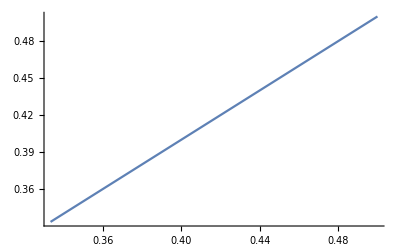

```mathematica
Plot[minIntervals[x]⟦1⟧,{x,1/3,1/2}]
```

```mathematica
Simplify[Eigenvalues[({{1-2r, 1/2-3/2 r+b ⅈ, 0}, {1/2-3/2 r-b ⅈ, r, 0}, {0, 0, r}})],{1/3≤r≤1/2,b∈Reals}]
```

{r,1/2 (1-√2 √(2 b^2+(1-3 r)^2)-r),1/2 (1+√2 √(2 b^2+(1-3 r)^2)-r)}

```mathematica
Reduce[{1-√2 √(2 b^2+(1-3 r)^2)-r≥0,1/3≤r≤1/2}]
```

(1/3≤r<(1+√2)/(1+3 √2)&&-1/2 √(-1+10 r-17 r^2)≤b≤1/2 √(-1+10 r-17 r^2))||(r==(1+√2)/(1+3 √2)&&b==0)

```mathematica
Simplify[(1+√2)/(1+3 √2)]
```

1/17 (5+2 √2)

```mathematica
N[{1/3,4/11,3/8,2/5,3/7,4/9,5/11,1/17 (5+2 √2),1/2}]
```

{0.333333,0.363636,0.375,0.4,0.428571,0.444444,0.454545,0.460496,0.5}

```mathematica
N[{4/11,5/11}]
```

{0.363636,0.454545}